3026.38

2533

22.3735

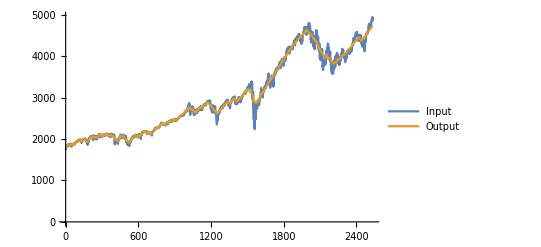

```mathematica
"input=Table[RandomInteger[{-20,20}],{i,1,20}]";
Evolve[l_,tolerance_]:=Module[{i,t=0,areChanges=True,Changes=List[],list=l,maxIterations=5000},
While[areChanges&&t<=maxIterations,
t++;
areChanges=False;
Changes=ConstantArray[0,Length[list]];
For[i=1,i<Length[list],i++,
If[list[[i]]-list[[i+1]]>=tolerance,
Changes[[i]]+=-1;
Changes[[i+1]]+=1;
areChanges=True,
If[list[[i]]-list[[i+1]]<=-tolerance,
Changes[[i]]+=1;
Changes[[i+1]]+=-1;
areChanges=True
]
]
];
"If[list[[-1]]>=tolerance,
Changes[[-1]]+=-1;
AppendTo[Changes,1];
AppendTo[list,0];
areChanges=True
]";
list=list+Changes;
];
Return[list]
]
N@Mean[input]
Length[input]
deriv=Table[Abs[input[[i+1]]-input[[i]]],{i,1,Length[input]-1}];
N@Mean[deriv]
ListLinePlot[{input,Evolve[input,4]},PlotLegends->{"Input","Output"}]
```

```mathematica
input={02/02/2024,4958.61,4916.06,4975.29,4907.99,02/01/2024,4906.19,4861.11,4906.97,4853.52,01/31/2024,4845.65,4899.19,4906.75,4845.15,01/30/2024,4924.97,4925.89,4931.09,4916.27,01/29/2024,4927.93,4892.95,4929.31,4887.40,01/26/2024,4890.97,4888.91,4906.69,4881.47,01/25/2024,4894.16,4886.66,4898.15,4869.34,01/24/2024,4868.55,4888.56,4903.68,4865.94,01/23/2024,4864.60,4856.80,4866.48,4844.37,01/22/2024,4850.43,4853.42,4868.41,4844.05,01/19/2024,4839.81,4796.28,4842.07,4785.87,01/18/2024,4780.94,4760.10,4785.79,4740.57,01/17/2024,4739.21,4739.13,4744.23,4714.82,01/16/2024,4765.98,4772.35,4782.34,4747.12,01/12/2024,4783.83,4791.18,4802.40,4768.98,01/11/2024,4780.24,4792.13,4798.50,4739.58,01/10/2024,4783.45,4759.94,4790.80,4756.20,01/09/2024,4756.50,4741.93,4765.47,4730.35,01/08/2024,4763.54,4703.70,4764.54,4699.82,01/05/2024,4697.24,4690.57,4721.49,4682.11,01/04/2024,4688.68,4697.42,4726.78,4687.53,01/03/2024,4704.81,4725.07,4729.29,4699.71,01/02/2024,4742.83,4745.20,4754.33,4722.67,12/29/2023,4769.83,4782.88,4788.43,4751.99,12/28/2023,4783.35,4786.44,4793.30,4780.98,12/27/2023,4781.58,4773.45,4785.39,4768.90,12/26/2023,4774.75,4758.86,4784.72,4758.45,12/22/2023,4754.63,4753.92,4772.94,4736.77,12/21/2023,4746.75,4724.29,4748.71,4708.35,12/20/2023,4698.35,4764.73,4778.01,4697.82,12/19/2023,4768.37,4743.72,4768.69,4743.72,12/18/2023,4740.56,4725.58,4749.52,4725.58,12/15/2023,4719.19,4714.23,4725.53,4704.69,12/14/2023,4719.55,4721.04,4738.57,4694.34,12/13/2023,4707.09,4646.20,4709.69,4643.23,12/12/2023,4643.70,4618.30,4643.93,4608.09,12/11/2023,4622.44,4593.39,4623.71,4593.39,12/08/2023,4604.37,4576.20,4609.23,4574.06,12/07/2023,4585.59,4568.84,4590.92,4565.22,12/06/2023,4549.34,4586.23,4590.74,4546.50,12/05/2023,4567.18,4557.25,4578.56,4551.68,12/04/2023,4569.78,4564.37,4572.37,4546.72,12/01/2023,4594.63,4559.43,4599.39,4554.71,11/30/2023,4567.80,4554.87,4569.89,4537.24,11/29/2023,4550.58,4571.84,4587.64,4547.15,11/28/2023,4554.89,4545.55,4568.14,4540.51,11/27/2023,4550.43,4554.86,4560.52,4546.32,11/24/2023,4559.34,4555.84,4560.31,4552.80,11/22/2023,4556.62,4553.04,4568.43,4545.05,11/21/2023,4538.19,4538.77,4542.14,4525.51,11/20/2023,4547.38,4511.70,4557.11,4510.36,11/17/2023,4514.02,4509.55,4520.12,4499.66,11/16/2023,4508.24,4497.08,4511.99,4487.83,11/15/2023,4502.88,4505.30,4521.17,4495.31,11/14/2023,4495.70,4458.97,4508.67,4458.97,11/13/2023,4411.55,4406.66,4421.76,4393.82,11/10/2023,4415.24,4364.15,4418.03,4353.34,11/09/2023,4347.35,4391.41,4393.40,4343.94,11/08/2023,4382.78,4384.37,4391.20,4359.76,11/07/2023,4378.38,4366.21,4386.26,4355.41,11/06/2023,4365.98,4364.27,4372.21,4347.53,11/03/2023,4358.34,4334.23,4373.62,4334.23,11/02/2023,4317.78,4268.26,4319.72,4268.26,11/01/2023,4237.86,4201.27,4245.64,4197.74,10/31/2023,4193.80,4171.33,4195.55,4153.12,10/30/2023,4166.82,4139.39,4177.47,4132.94,10/27/2023,4117.37,4152.93,4156.70,4103.78,10/26/2023,4137.23,4175.99,4183.60,4127.90,10/25/2023,4186.77,4232.42,4232.42,4181.42,10/24/2023,4247.68,4235.79,4259.38,4219.43,10/23/2023,4217.04,4210.40,4255.84,4189.22,10/20/2023,4224.16,4273.85,4276.56,4223.03,10/19/2023,4278.00,4321.36,4339.54,4269.69,10/18/2023,4314.60,4357.35,4364.20,4303.84,10/17/2023,4373.20,4345.23,4393.57,4337.54,10/16/2023,4373.63,4342.37,4383.33,4342.37,10/13/2023,4327.78,4360.49,4377.10,4311.97,10/12/2023,4349.61,4380.94,4385.85,4325.43,10/11/2023,4376.95,4366.59,4378.64,4345.34,10/10/2023,4358.24,4339.75,4385.46,4339.64,10/09/2023,4335.66,4289.02,4341.73,4283.79,10/06/2023,4308.50,4234.79,4324.10,4219.55,10/05/2023,4258.19,4259.31,4267.13,4225.91,10/04/2023,4263.75,4233.83,4268.50,4220.48,10/03/2023,4229.45,4269.75,4281.15,4216.45,10/02/2023,4288.39,4284.52,4300.58,4260.21,09/29/2023,4288.05,4328.18,4333.15,4274.86,09/28/2023,4299.70,4269.65,4317.27,4264.38,09/27/2023,4274.51,4282.63,4292.07,4238.63,09/26/2023,4273.53,4312.88,4313.01,4265.98,09/25/2023,4337.44,4310.62,4338.51,4302.70,09/22/2023,4320.06,4341.74,4357.40,4316.49,09/21/2023,4330.00,4374.36,4375.70,4329.17,09/20/2023,4402.20,4452.81,4461.03,4401.38,09/19/2023,4443.95,4445.41,4449.85,4416.61,09/18/2023,4453.53,4445.13,4466.36,4442.11,09/15/2023,4450.32,4497.98,4497.98,4447.21,09/14/2023,4505.10,4487.78,4511.99,4478.69,09/13/2023,4467.44,4462.65,4479.39,4453.52,09/12/2023,4461.90,4473.27,4487.11,4456.83,09/11/2023,4487.46,4480.98,4490.77,4467.89,09/08/2023,4457.49,4451.30,4473.53,4448.38,09/07/2023,4451.14,4434.55,4457.81,4430.46,09/06/2023,4465.48,4490.35,4490.35,4442.38,09/05/2023,4496.83,4510.06,4514.29,4496.01,09/01/2023,4515.77,4530.60,4541.25,4501.35,08/31/2023,4507.66,4517.01,4532.26,4507.39,08/30/2023,4514.87,4500.34,4521.65,4493.59,08/29/2023,4497.63,4432.75,4500.14,4431.68,08/28/2023,4433.31,4426.03,4439.56,4414.98,08/25/2023,4405.71,4389.38,4418.46,4356.29,08/24/2023,4376.31,4455.16,4458.30,4375.55,08/23/2023,4436.01,4396.44,4443.18,4396.44,08/22/2023,4387.55,4415.33,4418.59,4382.77,08/21/2023,4399.77,4380.28,4407.55,4360.30,08/18/2023,4369.71,4344.88,4381.82,4335.31,08/17/2023,4370.36,4416.32,4421.17,4364.83,08/16/2023,4404.33,4433.79,4449.95,4403.55,08/15/2023,4437.86,4478.87,4478.87,4432.19,08/14/2023,4489.72,4458.13,4490.33,4453.44,08/11/2023,4464.05,4450.69,4476.23,4443.98,08/10/2023,4468.83,4487.16,4527.37,4457.92,08/09/2023,4467.71,4501.57,4502.44,4461.33,08/08/2023,4499.38,4498.03,4503.31,4464.39,08/07/2023,4518.44,4491.58,4519.84,4491.15,08/04/2023,4478.03,4513.96,4540.34,4474.55,08/03/2023,4501.89,4494.27,4519.49,4485.54,08/02/2023,4513.39,4550.93,4550.93,4505.75,08/01/2023,4576.73,4578.83,4584.62,4567.53,07/31/2023,4588.96,4584.82,4594.22,4573.14,07/28/2023,4582.23,4565.75,4590.16,4564.01,07/27/2023,4537.41,4598.26,4607.07,4528.56,07/26/2023,4566.75,4558.96,4582.47,4547.58,07/25/2023,4567.46,4555.19,4580.62,4552.42,07/24/2023,4554.64,4543.39,4563.41,4541.29,07/21/2023,4536.34,4550.16,4555.00,4535.79,07/20/2023,4534.87,4554.38,4564.74,4527.56,07/19/2023,4565.72,4563.87,4578.43,4557.48,07/18/2023,4554.98,4521.78,4562.30,4514.59,07/17/2023,4522.79,4508.86,4532.85,4504.90,07/14/2023,4505.42,4514.61,4527.76,4499.56,07/13/2023,4510.04,4491.50,4517.38,4489.36,07/12/2023,4472.16,4467.69,4488.34,4463.23,07/11/2023,4439.26,4415.55,4443.64,4408.46,07/10/2023,4409.53,4394.23,4412.60,4389.92,07/07/2023,4398.95,4404.54,4440.39,4397.40,07/06/2023,4411.59,4422.62,4422.62,4385.05,07/05/2023,4446.82,4442.04,4454.06,4436.61,07/03/2023,4455.59,4450.48,4456.46,4442.29,06/30/2023,4450.38,4422.44,4458.48,4422.44,06/29/2023,4396.44,4374.94,4398.39,4371.97,06/28/2023,4376.86,4367.48,4390.35,4360.22,06/27/2023,4378.41,4337.36,4384.42,4335.00,06/26/2023,4328.82,4344.84,4362.06,4328.08,06/23/2023,4348.33,4354.17,4366.55,4341.34,06/22/2023,4381.89,4355.40,4382.25,4351.82,06/21/2023,4365.69,4380.01,4386.22,4360.14,06/20/2023,4388.71,4396.11,4400.15,4367.19,06/16/2023,4409.59,4440.95,4448.47,4407.44,06/15/2023,4425.84,4365.33,4439.20,4362.60,06/14/2023,4372.59,4366.29,4391.82,4337.85,06/13/2023,4369.01,4352.61,4375.37,4349.31,06/12/2023,4338.93,4308.32,4340.13,4304.37,06/09/2023,4298.86,4304.88,4322.62,4291.70,06/08/2023,4293.93,4268.69,4298.01,4261.07,06/07/2023,4267.52,4285.47,4299.19,4263.96,06/06/2023,4283.85,4271.34,4288.33,4263.09,06/05/2023,4273.79,4282.99,4299.28,4266.82,06/02/2023,4282.37,4241.01,4290.67,4241.01,06/01/2023,4221.02,4183.03,4232.43,4171.64,05/31/2023,4179.83,4190.74,4195.44,4166.15,05/30/2023,4205.52,4226.71,4231.10,4192.18,05/26/2023,4205.45,4156.16,4212.87,4156.16,05/25/2023,4151.28,4155.71,4165.74,4129.73,05/24/2023,4115.24,4132.96,4132.96,4103.98,05/23/2023,4145.58,4176.80,4185.68,4142.54,05/22/2023,4192.63,4190.78,4209.22,4179.68,05/19/2023,4191.98,4204.15,4212.91,4180.20,05/18/2023,4198.05,4157.68,4202.20,4153.50,05/17/2023,4158.77,4122.85,4164.67,4113.62,05/16/2023,4109.90,4127.95,4135.54,4109.86,05/15/2023,4136.28,4126.65,4141.25,4110.27,05/12/2023,4124.08,4138.54,4143.74,4099.12,05/11/2023,4130.62,4132.24,4132.80,4109.29,05/10/2023,4137.64,4143.74,4154.28,4098.92,05/09/2023,4119.17,4124.25,4130.35,4116.65,05/08/2023,4138.12,4136.98,4142.30,4123.81,05/05/2023,4136.25,4084.73,4147.02,4084.73,05/04/2023,4061.22,4082.55,4082.61,4048.28,05/03/2023,4090.75,4122.25,4148.30,4088.86,05/02/2023,4119.58,4164.10,4164.10,4089.72,05/01/2023,4167.87,4166.79,4186.92,4164.12,04/28/2023,4169.48,4129.63,4170.06,4127.18,04/27/2023,4135.35,4075.29,4138.24,4075.29,04/26/2023,4055.99,4087.78,4089.67,4049.35,04/25/2023,4071.63,4126.43,4126.43,4071.38,04/24/2023,4137.04,4132.07,4142.41,4117.77,04/21/2023,4133.52,4132.14,4138.02,4113.86,04/20/2023,4129.79,4130.48,4148.57,4114.57,04/19/2023,4154.52,4139.33,4162.57,4134.49,04/18/2023,4154.87,4164.26,4169.48,4140.36,04/17/2023,4151.32,4137.17,4151.72,4123.18,04/14/2023,4137.64,4140.11,4163.19,4113.20,04/13/2023,4146.22,4100.04,4150.26,4099.40,04/12/2023,4091.95,4121.72,4134.37,4086.94,04/11/2023,4108.94,4110.29,4124.26,4102.61,04/10/2023,4109.11,4085.20,4109.50,4072.55,04/06/2023,4105.02,4081.15,4107.32,4069.84,04/05/2023,4090.38,4094.50,4099.69,4072.56,04/04/2023,4100.60,4128.03,4133.13,4086.87,04/03/2023,4124.51,4102.20,4127.66,4098.79,03/31/2023,4109.31,4056.18,4110.75,4056.18,03/30/2023,4050.83,4046.74,4057.85,4032.10,03/29/2023,4027.81,3999.53,4030.59,3999.53,03/28/2023,3971.27,3974.13,3979.20,3951.53,03/27/2023,3977.53,3982.93,4003.83,3970.49,03/24/2023,3970.99,3939.21,3972.74,3909.16,03/23/2023,3948.72,3959.21,4007.66,3919.05,03/22/2023,3936.97,4002.04,4039.49,3936.17,03/21/2023,4002.87,3975.89,4009.08,3971.19,03/20/2023,3951.57,3917.47,3956.62,3916.89,03/17/2023,3916.64,3958.69,3958.91,3901.27,03/16/2023,3960.28,3878.93,3964.46,3864.11,03/15/2023,3891.93,3876.74,3894.26,3838.24,03/14/2023,3919.29,3894.01,3937.29,3873.63,03/13/2023,3855.76,3835.12,3905.05,3808.86,03/10/2023,3861.59,3912.77,3934.05,3846.32,03/09/2023,3918.32,3998.66,4017.81,3908.70,03/08/2023,3992.01,3987.55,4000.41,3969.76,03/07/2023,3986.37,4048.26,4050.00,3980.31,03/06/2023,4048.42,4055.15,4078.49,4044.61,03/03/2023,4045.64,3998.02,4048.29,3995.17,03/02/2023,3981.35,3938.68,3990.84,3928.16,03/01/2023,3951.39,3963.34,3971.73,3939.05,02/28/2023,3970.15,3977.19,3997.50,3968.98,02/27/2023,3982.24,3992.36,4018.05,3973.55,02/24/2023,3970.04,3973.24,3978.25,3943.08,02/23/2023,4012.32,4018.60,4028.30,3969.19,02/22/2023,3991.05,4001.83,4017.37,3976.90,02/21/2023,3997.34,4052.35,4052.35,3995.19,02/17/2023,4079.09,4077.39,4081.51,4047.95,02/16/2023,4090.41,4114.75,4136.54,4089.49,02/15/2023,4147.60,4119.50,4148.11,4103.98,02/14/2023,4136.13,4126.70,4159.77,4095.01,02/13/2023,4137.29,4096.62,4138.90,4092.67,02/10/2023,4090.46,4068.92,4094.36,4060.79,02/09/2023,4081.50,4144.25,4156.23,4069.67,02/08/2023,4117.86,4153.47,4156.85,4111.67,02/07/2023,4164.00,4105.35,4176.54,4088.39,02/06/2023,4111.08,4119.57,4124.63,4093.38,02/03/2023,4136.48,4136.69,4182.36,4123.36,02/02/2023,4179.76,4158.68,4195.44,4141.88,02/01/2023,4119.21,4070.07,4148.95,4037.20,01/31/2023,4076.60,4020.85,4077.16,4020.44,01/30/2023,4017.77,4049.27,4063.85,4015.55,01/27/2023,4070.56,4053.72,4094.21,4048.70,01/26/2023,4060.43,4036.08,4061.57,4013.29,01/25/2023,4016.22,3982.71,4019.55,3949.06,01/24/2023,4016.95,4001.74,4023.92,3989.79,01/23/2023,4019.81,3978.14,4039.31,3971.64,01/20/2023,3972.61,3909.04,3972.96,3897.86,01/19/2023,3898.85,3911.84,3922.94,3885.54,01/18/2023,3928.86,4002.25,4014.16,3926.59,01/17/2023,3990.97,3999.28,4015.39,3984.57,01/13/2023,3999.09,3960.60,4003.95,3947.67,01/12/2023,3983.17,3977.57,3997.76,3937.56,01/11/2023,3969.61,3932.35,3970.07,3928.54,01/10/2023,3919.25,3888.57,3919.83,3877.29,01/09/2023,3892.09,3910.82,3950.57,3890.42,01/06/2023,3895.08,3823.37,3906.19,3809.56,01/05/2023,3808.10,3839.74,3839.74,3802.42,01/04/2023,3852.97,3840.36,3873.16,3815.77,01/03/2023,3824.14,3853.29,3878.46,3794.33,12/30/2022,3839.50,3829.06,3839.85,3800.34,12/29/2022,3849.28,3805.45,3858.19,3805.45,12/28/2022,3783.22,3829.56,3848.32,3780.78,12/27/2022,3829.25,3843.34,3846.65,3813.22,12/23/2022,3844.82,3815.11,3845.80,3797.01,12/22/2022,3822.39,3853.26,3853.26,3764.49,12/21/2022,3878.44,3839.49,3889.82,3839.49,12/20/2022,3821.62,3810.47,3838.24,3795.62,12/19/2022,3817.66,3853.79,3854.86,3800.04,12/16/2022,3852.36,3890.91,3890.91,3827.91,12/15/2022,3895.75,3958.37,3958.37,3879.45,12/14/2022,3995.32,4015.54,4053.76,3965.65,12/13/2022,4019.65,4069.38,4100.96,3993.03,12/12/2022,3990.56,3939.29,3990.71,3935.30,12/09/2022,3934.38,3954.17,3977.02,3933.04,12/08/2022,3963.51,3947.79,3974.19,3935.83,12/07/2022,3933.92,3933.28,3957.57,3922.68,12/06/2022,3941.26,3996.63,4001.51,3918.39,12/05/2022,3998.84,4052.02,4052.45,3984.49,12/02/2022,4071.70,4040.17,4080.48,4026.63,12/01/2022,4076.57,4087.14,4100.51,4050.87,11/30/2022,4080.11,3957.18,4080.11,3938.58,11/29/2022,3957.63,3964.19,3976.77,3937.65,11/28/2022,3963.94,4005.36,4012.27,3955.77,11/25/2022,4026.12,4023.34,4034.02,4020.76,11/23/2022,4027.26,4000.30,4033.78,3998.66,11/22/2022,4003.58,3965.51,4005.88,3956.88,11/21/2022,3949.94,3956.23,3962.00,3933.34,11/18/2022,3965.34,3966.39,3979.89,3935.98,11/17/2022,3946.56,3919.26,3954.33,3906.54,11/16/2022,3958.79,3976.82,3983.09,3954.34,11/15/2022,3991.73,4006.41,4028.84,3953.17,11/14/2022,3957.25,3977.97,4008.97,3956.40,11/11/2022,3992.93,3963.72,4001.48,3944.82,11/10/2022,3956.37,3859.89,3958.33,3859.89,11/09/2022,3748.57,3810.94,3818.20,3744.22,11/08/2022,3828.11,3817.02,3859.40,3786.28,11/07/2022,3806.80,3780.71,3813.95,3764.70,11/04/2022,3770.55,3766.98,3796.34,3708.84,11/03/2022,3719.89,3733.25,3750.59,3698.15,11/02/2022,3759.69,3852.90,3894.44,3758.68,11/01/2022,3856.10,3901.79,3911.79,3843.80,10/31/2022,3871.98,3881.85,3893.73,3863.18,10/28/2022,3901.06,3808.26,3905.42,3808.26,10/27/2022,3807.30,3834.69,3859.95,3803.79,10/26/2022,3830.60,3825.97,3886.15,3824.07,10/25/2022,3859.11,3799.44,3862.85,3799.44,10/24/2022,3797.34,3762.01,3810.74,3741.65,10/21/2022,3752.75,3657.10,3757.89,3647.42,10/20/2022,3665.78,3689.05,3736.00,3656.44,10/19/2022,3695.16,3703.11,3728.58,3666.51,10/18/2022,3719.98,3746.26,3762.79,3686.53,10/17/2022,3677.95,3638.65,3689.73,3638.65,10/14/2022,3583.07,3690.41,3712.00,3579.68,10/13/2022,3669.91,3520.37,3685.41,3491.58,10/12/2022,3577.03,3590.83,3608.34,3573.86,10/11/2022,3588.84,3595.86,3640.66,3568.45,10/10/2022,3612.39,3647.51,3652.17,3588.10,10/07/2022,3639.66,3706.74,3706.74,3620.73,10/06/2022,3744.52,3771.97,3797.93,3739.22,10/05/2022,3783.28,3753.25,3806.91,3722.66,10/04/2022,3790.93,3726.46,3791.92,3726.46,10/03/2022,3678.43,3609.78,3698.35,3604.93,09/30/2022,3585.62,3633.48,3671.44,3584.13,09/29/2022,3640.47,3687.01,3687.01,3610.40,09/28/2022,3719.04,3651.94,3736.74,3640.61,09/27/2022,3647.29,3686.44,3717.53,3623.29,09/26/2022,3655.04,3682.72,3715.67,3644.76,09/23/2022,3693.23,3727.14,3727.14,3647.47,09/22/2022,3757.99,3782.36,3790.90,3749.45,09/21/2022,3789.93,3871.40,3907.07,3789.49,09/20/2022,3855.93,3875.23,3876.01,3827.54,09/19/2022,3899.89,3849.91,3900.45,3838.50,09/16/2022,3873.33,3880.95,3880.95,3837.08,09/15/2022,3901.35,3932.41,3959.14,3888.28,09/14/2022,3946.01,3940.73,3961.94,3912.18,09/13/2022,3932.69,4037.12,4037.12,3921.28,09/12/2022,4110.41,4083.67,4119.28,4083.67,09/09/2022,4067.36,4022.94,4076.81,4022.94,09/08/2022,4006.18,3959.94,4010.50,3944.81,09/07/2022,3979.87,3909.43,3987.89,3906.03,09/06/2022,3908.19,3930.89,3942.55,3886.75,09/02/2022,3924.26,3994.66,4018.43,3906.21,09/01/2022,3966.85,3936.73,3970.23,3903.65,08/31/2022,3955.00,4000.67,4015.37,3954.53,08/30/2022,3986.16,4041.25,4044.98,3965.21,08/29/2022,4030.61,4034.58,4062.99,4017.42,08/26/2022,4057.66,4198.74,4203.04,4057.66,08/25/2022,4199.12,4153.26,4200.54,4147.59,08/24/2022,4140.77,4126.55,4156.56,4119.97,08/23/2022,4128.73,4133.09,4159.77,4124.03,08/22/2022,4137.99,4195.08,4195.08,4129.86,08/19/2022,4228.48,4266.31,4266.31,4218.70,08/18/2022,4283.74,4273.13,4292.53,4261.98,08/17/2022,4274.04,4280.40,4302.18,4253.08,08/16/2022,4305.20,4290.46,4325.28,4277.77,08/15/2022,4297.14,4269.37,4301.79,4256.90,08/12/2022,4280.15,4225.02,4280.47,4219.78,08/11/2022,4207.27,4227.40,4257.91,4201.41,08/10/2022,4210.24,4181.02,4211.03,4177.26,08/09/2022,4122.47,4133.11,4137.30,4112.09,08/08/2022,4140.06,4155.93,4186.62,4128.97,08/05/2022,4145.19,4115.87,4151.58,4107.31,08/04/2022,4151.94,4154.85,4161.29,4135.42,08/03/2022,4155.17,4107.96,4167.66,4107.96,08/02/2022,4091.19,4104.21,4140.47,4079.81,08/01/2022,4118.63,4112.38,4144.95,4096.02,07/29/2022,4130.29,4087.33,4140.15,4079.22,07/28/2022,4072.43,4026.13,4078.95,3992.97,07/27/2022,4023.61,3951.43,4039.56,3951.43,07/26/2022,3921.05,3953.22,3953.22,3910.74,07/25/2022,3966.84,3965.72,3975.30,3943.46,07/22/2022,3961.63,3998.43,4012.44,3938.86,07/21/2022,3998.95,3955.47,3999.29,3927.64,07/20/2022,3959.90,3935.32,3974.13,3922.03,07/19/2022,3936.69,3860.73,3939.81,3860.73,07/18/2022,3830.85,3883.79,3902.44,3818.63,07/15/2022,3863.16,3818.00,3863.62,3817.18,07/14/2022,3790.38,3763.99,3796.41,3721.56,07/13/2022,3801.78,3779.67,3829.44,3759.07,07/12/2022,3818.80,3851.95,3873.41,3802.36,07/11/2022,3854.43,3880.94,3880.94,3847.22,07/08/2022,3899.38,3888.26,3918.50,3869.34,07/07/2022,3902.62,3858.85,3910.63,3858.85,07/06/2022,3845.08,3831.98,3870.91,3809.37,07/05/2022,3831.39,3792.61,3832.19,3742.06,07/01/2022,3825.33,3781.00,3829.82,3752.10,06/30/2022,3785.38,3785.99,3818.99,3738.67,06/29/2022,3818.83,3825.09,3836.50,3799.02,06/28/2022,3821.55,3913.00,3945.86,3820.14,06/27/2022,3900.11,3920.76,3927.72,3889.66,06/24/2022,3911.74,3821.75,3913.65,3821.75,06/23/2022,3795.73,3774.71,3802.58,3743.52,06/22/2022,3759.89,3733.89,3801.79,3717.69,06/21/2022,3764.79,3715.31,3779.65,3715.31,06/17/2022,3674.84,3665.90,3707.71,3636.87,06/16/2022,3666.77,3728.18,3728.18,3639.77,06/15/2022,3789.99,3764.05,3837.56,3722.30,06/14/2022,3735.48,3763.52,3778.18,3705.68,06/13/2022,3749.63,3838.15,3838.15,3734.30,06/10/2022,3900.86,3974.39,3974.39,3900.16,06/09/2022,4017.82,4101.65,4119.10,4017.17,06/08/2022,4115.77,4147.12,4160.14,4107.20,06/07/2022,4160.68,4096.47,4164.86,4080.19,06/06/2022,4121.43,4134.72,4168.78,4109.18,06/03/2022,4108.54,4137.57,4142.67,4098.67,06/02/2022,4176.82,4095.41,4177.51,4074.37,06/01/2022,4101.23,4149.78,4166.54,4073.85,05/31/2022,4132.15,4151.09,4168.34,4104.88,05/27/2022,4158.24,4077.43,4158.49,4077.43,05/26/2022,4057.84,3984.60,4075.14,3984.60,05/25/2022,3978.73,3929.59,3999.33,3925.03,05/24/2022,3941.48,3942.94,3955.68,3875.13,05/23/2022,3973.75,3927.02,3981.88,3909.04,05/20/2022,3901.36,3927.76,3943.42,3810.32,05/19/2022,3900.79,3899.00,3945.96,3876.58,05/18/2022,3923.68,4051.98,4051.98,3911.91,05/17/2022,4088.85,4052.00,4090.72,4033.93,05/16/2022,4008.01,4013.02,4046.46,3983.99,05/13/2022,4023.89,3963.90,4038.88,3963.90,05/12/2022,3930.08,3903.95,3964.80,3858.87,05/11/2022,3935.18,3990.08,4049.09,3928.82,05/10/2022,4001.05,4035.18,4068.82,3958.17,05/09/2022,3991.24,4081.27,4081.27,3975.48,05/06/2022,4123.34,4128.17,4157.69,4067.91,05/05/2022,4146.87,4270.43,4270.43,4106.01,05/04/2022,4300.17,4181.18,4307.66,4148.91,05/03/2022,4175.48,4159.78,4200.10,4147.08,05/02/2022,4155.38,4130.61,4169.81,4062.51,04/29/2022,4131.93,4253.75,4269.68,4124.28,04/28/2022,4287.50,4222.58,4308.45,4188.63,04/27/2022,4183.96,4186.52,4240.71,4162.90,04/26/2022,4175.20,4278.14,4278.14,4175.04,04/25/2022,4296.12,4255.34,4299.02,4200.82,04/22/2022,4271.78,4385.83,4385.83,4267.62,04/21/2022,4393.66,4489.17,4512.94,4384.47,04/20/2022,4459.45,4472.26,4488.29,4448.76,04/19/2022,4462.21,4390.63,4471.03,4390.63,04/18/2022,4391.69,4385.63,4410.31,4370.30,04/14/2022,4392.59,4449.12,4460.46,4390.77,04/13/2022,4446.59,4394.30,4453.92,4392.70,04/12/2022,4397.45,4437.59,4471.00,4381.34,04/11/2022,4412.53,4462.64,4464.35,4408.38,04/08/2022,4488.28,4494.15,4520.41,4474.60,04/07/2022,4500.21,4474.65,4521.16,4450.30,04/06/2022,4481.15,4494.17,4503.94,4450.04,04/05/2022,4525.12,4572.45,4593.45,4514.17,04/04/2022,4582.64,4547.97,4583.50,4539.21,04/01/2022,4545.86,4540.32,4548.70,4507.57,03/31/2022,4530.41,4599.02,4603.07,4530.41,03/30/2022,4602.45,4624.20,4627.77,4581.32,03/29/2022,4631.60,4602.86,4637.30,4589.66,03/28/2022,4575.52,4541.09,4575.65,4517.69,03/25/2022,4543.06,4522.91,4546.03,4501.07,03/24/2022,4520.16,4469.98,4520.58,4465.17,03/23/2022,4456.24,4493.10,4501.07,4455.81,03/22/2022,4511.61,4469.10,4522.00,4469.10,03/21/2022,4461.18,4462.40,4481.75,4424.30,03/18/2022,4463.12,4407.34,4465.40,4390.57,03/17/2022,4411.67,4345.11,4412.67,4335.65,03/16/2022,4357.86,4288.14,4358.90,4251.99,03/15/2022,4262.45,4188.82,4271.05,4187.90,03/14/2022,4173.11,4202.75,4247.57,4161.72,03/11/2022,4204.31,4279.50,4291.01,4200.49,03/10/2022,4259.52,4252.55,4268.28,4209.80,03/09/2022,4277.88,4223.10,4299.40,4223.10,03/08/2022,4170.70,4202.66,4276.94,4157.87,03/07/2022,4201.09,4327.01,4327.01,4199.85,03/04/2022,4328.87,4342.12,4342.12,4284.98,03/03/2022,4363.49,4401.31,4416.78,4345.56,03/02/2022,4386.54,4322.56,4401.48,4322.56,03/01/2022,4306.26,4363.14,4378.45,4279.54,02/28/2022,4373.94,4354.17,4388.84,4315.12,02/25/2022,4384.65,4298.38,4385.34,4286.83,02/24/2022,4288.70,4155.77,4294.73,4114.65,02/23/2022,4225.50,4324.93,4341.51,4221.51,02/22/2022,4304.76,4332.74,4362.12,4267.11,02/18/2022,4348.87,4384.57,4394.60,4327.22,02/17/2022,4380.26,4456.06,4456.06,4373.81,02/16/2022,4475.01,4455.75,4489.55,4429.68,02/15/2022,4471.07,4429.28,4472.77,4429.28,02/14/2022,4401.67,4412.61,4426.22,4364.84,02/11/2022,4418.64,4506.27,4526.33,4401.41,02/10/2022,4504.08,4553.24,4588.92,4484.31,02/09/2022,4587.18,4547.00,4590.03,4547.00,02/08/2022,4521.54,4480.02,4531.32,4465.40,02/07/2022,4483.87,4505.75,4521.86,4471.47,02/04/2022,4500.53,4482.79,4539.66,4451.50,02/03/2022,4477.44,4535.41,4542.88,4470.39,02/02/2022,4589.38,4566.39,4595.31,4544.32,02/01/2022,4546.54,4519.57,4550.49,4483.53,01/31/2022,4515.55,4431.79,4516.89,4414.02,01/28/2022,4431.85,4336.19,4432.72,4292.46,01/27/2022,4326.51,4380.58,4428.74,4309.50,01/26/2022,4349.93,4408.43,4453.23,4304.80,01/25/2022,4356.45,4366.64,4411.01,4287.11,01/24/2022,4410.13,4356.32,4417.35,4222.62,01/21/2022,4397.94,4471.38,4494.52,4395.34,01/20/2022,4482.73,4547.35,4602.11,4477.95,01/19/2022,4532.76,4588.03,4611.55,4530.20,01/18/2022,4577.11,4632.24,4632.24,4568.70,01/14/2022,4662.85,4637.99,4665.13,4614.75,01/13/2022,4659.03,4733.56,4744.13,4650.29,01/12/2022,4726.35,4728.59,4748.83,4706.71,01/11/2022,4713.07,4669.14,4714.13,4638.27,01/10/2022,4670.29,4655.34,4673.02,4582.24,01/07/2022,4677.03,4697.66,4707.95,4662.74,01/06/2022,4696.05,4693.39,4725.01,4671.26,01/05/2022,4700.58,4787.99,4797.70,4699.44,01/04/2022,4793.54,4804.51,4818.62,4774.27,01/03/2022,4796.56,4778.14,4796.64,4758.17,12/31/2021,4766.18,4775.21,4786.83,4765.75,12/30/2021,4778.73,4794.23,4808.93,4775.33,12/29/2021,4793.06,4788.64,4804.06,4778.08,12/28/2021,4786.35,4795.49,4807.02,4780.04,12/27/2021,4791.19,4733.99,4791.49,4733.99,12/23/2021,4725.79,4703.96,4740.74,4703.96,12/22/2021,4696.56,4650.36,4697.67,4645.53,12/21/2021,4649.23,4594.96,4651.14,4583.16,12/20/2021,4568.02,4587.90,4587.90,4531.10,12/17/2021,4620.64,4652.50,4666.70,4600.22,12/16/2021,4668.67,4719.13,4731.99,4651.89,12/15/2021,4709.85,4636.46,4712.60,4611.22,12/14/2021,4634.09,4642.99,4660.47,4606.52,12/13/2021,4668.97,4710.30,4710.30,4667.60,12/10/2021,4712.02,4687.64,4713.57,4670.24,12/09/2021,4667.45,4691.00,4695.26,4665.98,12/08/2021,4701.21,4690.86,4705.06,4674.52,12/07/2021,4686.75,4631.97,4694.04,4631.97,12/06/2021,4591.67,4548.37,4612.60,4540.51,12/03/2021,4538.43,4589.49,4608.03,4495.12,12/02/2021,4577.10,4504.73,4595.46,4504.73,12/01/2021,4513.04,4602.82,4652.94,4510.27,11/30/2021,4567.00,4640.25,4646.02,4560.00,11/29/2021,4655.27,4628.75,4672.95,4625.26,11/26/2021,4594.62,4664.63,4664.63,4585.43,11/24/2021,4701.46,4675.78,4702.87,4659.89,11/23/2021,4690.70,4678.48,4699.39,4652.66,11/22/2021,4682.94,4712.00,4743.83,4682.17,11/19/2021,4697.96,4708.44,4717.75,4694.22,11/18/2021,4704.54,4700.72,4708.80,4672.78,11/17/2021,4688.67,4701.50,4701.50,4684.41,11/16/2021,4700.90,4679.42,4714.95,4679.42,11/15/2021,4682.80,4689.30,4697.42,4672.86,11/12/2021,4682.85,4655.24,4688.47,4650.77,11/11/2021,4649.27,4659.39,4664.55,4648.31,11/10/2021,4646.71,4670.26,4684.85,4630.86,11/09/2021,4685.25,4707.25,4708.53,4670.87,11/08/2021,4701.70,4701.48,4714.92,4694.39,11/05/2021,4697.53,4699.26,4718.50,4681.32,11/04/2021,4680.06,4662.93,4683.00,4662.59,11/03/2021,4660.57,4630.65,4663.46,4621.19,11/02/2021,4630.65,4613.34,4635.15,4613.34,11/01/2021,4613.67,4610.62,4620.34,4595.06,10/29/2021,4605.38,4572.87,4608.08,4567.59,10/28/2021,4596.42,4562.84,4597.55,4562.84,10/27/2021,4551.68,4580.22,4584.57,4551.66,10/26/2021,4574.79,4578.69,4598.53,4569.17,10/25/2021,4566.48,4553.69,4572.62,4537.36,10/22/2021,4544.90,4546.12,4559.67,4524.00,10/21/2021,4549.78,4532.24,4551.44,4526.89,10/20/2021,4536.19,4524.42,4540.87,4524.40,10/19/2021,4519.63,4497.34,4520.40,4496.41,10/18/2021,4486.46,4463.72,4488.75,4447.47,10/15/2021,4471.37,4447.69,4475.82,4447.69,10/14/2021,4438.26,4386.75,4439.73,4386.75,10/13/2021,4363.80,4358.01,4372.87,4329.92,10/12/2021,4350.65,4368.31,4374.89,4342.09,10/11/2021,4361.19,4385.44,4415.88,4360.59,10/08/2021,4391.34,4406.51,4412.02,4386.22,10/07/2021,4399.76,4383.73,4429.97,4383.73,10/06/2021,4363.55,4319.57,4365.57,4290.49,10/05/2021,4345.72,4309.87,4369.23,4309.87,10/04/2021,4300.46,4348.84,4355.51,4278.94,10/01/2021,4357.04,4317.16,4375.19,4288.52,09/30/2021,4307.54,4370.67,4382.55,4306.24,09/29/2021,4359.46,4362.41,4385.57,4355.08,09/28/2021,4352.63,4419.54,4419.54,4346.33,09/27/2021,4443.11,4442.12,4457.30,4436.19,09/24/2021,4455.48,4438.04,4463.12,4430.27,09/23/2021,4448.98,4406.75,4465.40,4406.75,09/22/2021,4395.64,4367.43,4416.75,4367.43,09/21/2021,4354.19,4374.45,4394.87,4347.96,09/20/2021,4357.73,4402.95,4402.95,4305.91,09/17/2021,4432.99,4469.74,4471.52,4427.76,09/16/2021,4473.75,4477.09,4485.87,4443.80,09/15/2021,4480.70,4447.49,4486.87,4438.37,09/14/2021,4443.05,4479.33,4485.68,4435.46,09/13/2021,4468.73,4474.81,4492.99,4445.70,09/10/2021,4458.58,4506.92,4520.47,4457.66,09/09/2021,4493.28,4513.02,4529.90,4492.07,09/08/2021,4514.07,4518.09,4521.79,4493.95,09/07/2021,4520.03,4535.38,4535.38,4513.00,09/03/2021,4535.43,4532.42,4541.45,4521.30,09/02/2021,4536.95,4534.48,4545.85,4524.66,09/01/2021,4524.09,4528.80,4537.11,4522.02,08/31/2021,4522.68,4529.75,4531.39,4515.80,08/30/2021,4528.79,4513.76,4537.36,4513.76,08/27/2021,4509.37,4474.10,4513.33,4474.10,08/26/2021,4470.00,4493.75,4495.90,4468.99,08/25/2021,4496.19,4490.45,4501.71,4485.66,08/24/2021,4486.23,4484.40,4492.81,4482.28,08/23/2021,4479.53,4450.29,4489.88,4450.29,08/20/2021,4441.67,4410.56,4444.35,4406.80,08/19/2021,4405.80,4382.44,4418.61,4367.73,08/18/2021,4400.27,4440.94,4454.32,4397.59,08/17/2021,4448.08,4462.12,4462.12,4417.83,08/16/2021,4479.71,4461.65,4480.26,4437.66,08/13/2021,4468.00,4464.84,4468.37,4460.82,08/12/2021,4460.83,4446.08,4461.77,4435.96,08/11/2021,4447.70,4442.18,4449.44,4436.42,08/10/2021,4436.75,4435.79,4445.21,4430.03,08/09/2021,4432.35,4437.77,4439.39,4424.74,08/06/2021,4436.52,4429.07,4440.82,4429.07,08/05/2021,4429.10,4408.86,4429.76,4408.86,08/04/2021,4402.66,4415.95,4416.17,4400.23,08/03/2021,4423.15,4392.74,4423.79,4373.00,08/02/2021,4387.16,4406.86,4422.18,4384.81,07/30/2021,4395.26,4395.12,4412.25,4389.65,07/29/2021,4419.15,4403.59,4429.97,4403.59,07/28/2021,4400.64,4402.95,4415.47,4387.01,07/27/2021,4401.46,4416.38,4416.38,4372.51,07/26/2021,4422.30,4409.58,4422.73,4405.45,07/23/2021,4411.79,4381.20,4415.18,4381.20,07/22/2021,4367.48,4361.27,4369.87,4350.06,07/21/2021,4358.69,4331.13,4359.70,4331.13,07/20/2021,4323.06,4265.11,4336.84,4262.05,07/19/2021,4258.49,4296.40,4296.40,4233.13,07/16/2021,4327.16,4367.43,4375.09,4322.53,07/15/2021,4360.03,4369.02,4369.02,4340.70,07/14/2021,4374.30,4380.11,4393.68,4362.36,07/13/2021,4369.21,4381.07,4392.37,4366.92,07/12/2021,4384.63,4372.41,4386.68,4364.03,07/09/2021,4369.55,4329.38,4371.60,4329.38,07/08/2021,4320.82,4321.07,4330.88,4289.37,07/07/2021,4358.13,4351.01,4361.88,4329.79,07/06/2021,4343.54,4356.46,4356.46,4314.37,07/02/2021,4352.34,4326.60,4355.43,4326.60,07/01/2021,4319.94,4300.73,4320.66,4300.73,06/30/2021,4297.50,4290.65,4302.43,4287.96,06/29/2021,4291.80,4293.21,4300.52,4287.04,06/28/2021,4290.61,4284.90,4292.14,4274.67,06/25/2021,4280.70,4274.45,4286.12,4271.16,06/24/2021,4266.49,4256.97,4271.28,4256.97,06/23/2021,4241.84,4249.27,4256.60,4241.43,06/22/2021,4246.44,4224.61,4255.84,4217.27,06/21/2021,4224.79,4173.40,4226.24,4173.40,06/18/2021,4166.45,4204.78,4204.78,4164.40,06/17/2021,4221.86,4220.37,4232.29,4196.05,06/16/2021,4223.70,4248.87,4251.89,4202.45,06/15/2021,4246.59,4255.28,4257.16,4238.35,06/14/2021,4255.15,4248.31,4255.59,4234.07,06/11/2021,4247.44,4242.90,4248.38,4232.25,06/10/2021,4239.18,4228.56,4249.74,4220.34,06/09/2021,4219.55,4232.99,4237.09,4218.74,06/08/2021,4227.26,4233.81,4236.74,4208.41,06/07/2021,4226.52,4229.34,4232.34,4215.66,06/04/2021,4229.89,4206.05,4233.45,4206.05,06/03/2021,4192.85,4191.43,4204.39,4167.93,06/02/2021,4208.12,4206.82,4217.37,4198.27,06/01/2021,4202.04,4216.52,4234.12,4197.59,05/28/2021,4204.11,4210.77,4218.36,4203.57,05/27/2021,4200.88,4201.94,4213.38,4197.78,05/26/2021,4195.99,4191.59,4202.61,4184.11,05/25/2021,4188.13,4205.94,4213.42,4182.52,05/24/2021,4197.05,4170.16,4209.52,4170.16,05/21/2021,4155.86,4168.61,4188.72,4151.72,05/20/2021,4159.12,4121.97,4172.80,4121.97,05/19/2021,4115.68,4098.45,4116.93,4061.41,05/18/2021,4127.83,4165.94,4169.15,4125.99,05/17/2021,4163.29,4169.92,4171.92,4142.69,05/14/2021,4173.85,4129.58,4183.13,4129.58,05/13/2021,4112.50,4074.99,4131.58,4074.99,05/12/2021,4063.04,4130.55,4134.73,4056.88,05/11/2021,4152.10,4150.34,4162.04,4111.53,05/10/2021,4188.43,4228.29,4236.39,4188.13,05/07/2021,4232.60,4210.34,4238.04,4201.64,05/06/2021,4201.62,4169.14,4202.70,4147.33,05/05/2021,4167.59,4177.06,4187.72,4160.94,05/04/2021,4164.66,4179.04,4179.04,4128.59,05/03/2021,4192.66,4191.98,4209.39,4188.03,04/30/2021,4181.17,4198.10,4198.10,4174.85,04/29/2021,4211.47,4206.14,4218.78,4176.81,04/28/2021,4183.18,4185.14,4201.53,4181.78,04/27/2021,4186.72,4188.25,4193.35,4176.22,04/26/2021,4187.62,4185.03,4194.19,4182.36,04/23/2021,4180.17,4138.78,4194.17,4138.78,04/22/2021,4134.98,4170.46,4179.57,4123.69,04/21/2021,4173.42,4128.42,4175.02,4126.35,04/20/2021,4134.94,4159.18,4159.18,4118.38,04/19/2021,4163.26,4179.80,4180.81,4150.47,04/16/2021,4185.47,4174.14,4191.31,4170.75,04/15/2021,4170.42,4139.76,4173.49,4139.76,04/14/2021,4124.66,4143.25,4151.69,4120.87,04/13/2021,4141.59,4130.10,4148.00,4124.43,04/12/2021,4127.99,4124.71,4131.76,4114.82,04/09/2021,4128.80,4096.11,4129.48,4095.51,04/08/2021,4097.17,4089.95,4098.19,4082.54,04/07/2021,4079.95,4074.29,4083.13,4068.31,04/06/2021,4073.94,4075.57,4086.23,4068.14,04/05/2021,4077.91,4034.44,4083.42,4034.44,04/01/2021,4019.87,3992.78,4020.63,3992.78,03/31/2021,3972.89,3967.25,3994.41,3966.98,03/30/2021,3958.55,3963.34,3968.01,3944.35,03/29/2021,3971.09,3969.31,3981.83,3943.25,03/26/2021,3974.54,3917.12,3978.19,3917.12,03/25/2021,3909.52,3879.34,3919.54,3853.50,03/24/2021,3889.14,3919.93,3942.08,3889.07,03/23/2021,3910.52,3937.60,3949.13,3901.57,03/22/2021,3940.59,3916.48,3955.31,3914.16,03/19/2021,3913.10,3913.14,3930.12,3886.75,03/18/2021,3915.46,3953.50,3969.62,3910.86,03/17/2021,3974.12,3949.57,3983.87,3935.74,03/16/2021,3962.71,3973.59,3981.04,3953.44,03/15/2021,3968.94,3942.96,3970.08,3923.54,03/12/2021,3943.34,3924.52,3944.99,3915.21,03/11/2021,3939.34,3915.54,3960.27,3915.54,03/10/2021,3898.81,3891.99,3917.35,3885.73,03/09/2021,3875.44,3851.93,3903.76,3851.93,03/08/2021,3821.35,3844.39,3881.06,3819.25,03/05/2021,3841.94,3793.58,3851.69,3730.19,03/04/2021,3768.47,3818.53,3843.67,3723.34,03/03/2021,3819.72,3863.99,3874.47,3818.86,03/02/2021,3870.29,3903.64,3906.41,3868.57,03/01/2021,3901.82,3842.51,3914.50,3842.51,02/26/2021,3811.15,3839.66,3861.08,3789.54,02/25/2021,3829.34,3915.80,3925.02,3814.04,02/24/2021,3925.43,3873.71,3928.65,3859.60,02/23/2021,3881.37,3857.07,3895.98,3805.59,02/22/2021,3876.50,3885.55,3902.92,3874.71,02/19/2021,3906.71,3921.16,3930.41,3903.07,02/18/2021,3913.97,3915.86,3921.98,3885.03,02/17/2021,3931.33,3918.50,3933.61,3900.43,02/16/2021,3932.59,3939.61,3950.43,3923.85,02/12/2021,3934.83,3911.65,3937.23,3905.78,02/11/2021,3916.38,3916.40,3925.99,3890.39,02/10/2021,3909.88,3920.78,3931.50,3884.94,02/09/2021,3911.23,3910.49,3918.35,3902.64,02/08/2021,3915.59,3892.59,3915.77,3892.59,02/05/2021,3886.83,3878.30,3894.56,3874.93,02/04/2021,3871.74,3836.66,3872.42,3836.66,02/03/2021,3830.17,3840.27,3847.51,3816.68,02/02/2021,3826.31,3791.84,3843.09,3791.84,02/01/2021,3773.86,3731.17,3784.32,3725.62,01/29/2021,3714.24,3778.05,3778.05,3694.12,01/28/2021,3787.38,3755.75,3830.50,3755.75,01/27/2021,3750.77,3836.83,3836.83,3732.48,01/26/2021,3849.62,3862.96,3870.90,3847.78,01/25/2021,3855.36,3851.68,3859.23,3797.16,01/22/2021,3841.47,3844.24,3852.31,3830.41,01/21/2021,3853.07,3857.46,3861.45,3845.05,01/20/2021,3851.85,3816.22,3859.75,3816.22,01/19/2021,3798.91,3781.88,3804.53,3780.37,01/15/2021,3768.25,3788.73,3788.73,3749.62,01/14/2021,3795.54,3814.98,3823.60,3792.86,01/13/2021,3809.84,3802.23,3820.96,3791.50,01/12/2021,3801.19,3801.62,3810.78,3776.51,01/11/2021,3799.61,3803.14,3817.86,3789.02,01/08/2021,3824.68,3815.05,3826.69,3783.60,01/07/2021,3803.79,3764.71,3811.55,3764.71,01/06/2021,3748.14,3712.20,3783.04,3705.34,01/05/2021,3726.86,3698.02,3737.83,3695.07,01/04/2021,3700.65,3764.61,3769.99,3662.71,12/31/2020,3756.07,3733.27,3760.20,3726.88,12/30/2020,3732.04,3736.19,3744.63,3730.21,12/29/2020,3727.04,3750.01,3756.12,3723.31,12/28/2020,3735.36,3723.03,3740.51,3723.03,12/24/2020,3703.06,3694.03,3703.82,3689.32,12/23/2020,3690.01,3693.42,3711.24,3689.28,12/22/2020,3687.26,3698.08,3698.26,3676.16,12/21/2020,3694.92,3684.28,3702.90,3636.48,12/18/2020,3709.41,3722.39,3726.70,3685.84,12/17/2020,3722.48,3713.65,3725.12,3710.87,12/16/2020,3701.17,3696.25,3711.27,3688.57,12/15/2020,3694.62,3666.41,3695.29,3659.62,12/14/2020,3647.49,3675.27,3697.61,3645.84,12/11/2020,3663.46,3656.08,3665.91,3633.40,12/10/2020,3668.10,3659.13,3678.49,3645.18,12/09/2020,3672.82,3705.98,3712.39,3660.54,12/08/2020,3702.25,3683.05,3708.45,3678.83,12/07/2020,3691.96,3694.73,3697.41,3678.88,12/04/2020,3699.12,3670.94,3699.20,3670.94,12/03/2020,3666.72,3668.28,3682.73,3657.17,12/02/2020,3669.01,3653.78,3670.96,3644.84,12/01/2020,3662.45,3645.87,3678.45,3645.87,11/30/2020,3621.63,3634.18,3634.18,3594.39,11/27/2020,3638.35,3638.55,3644.31,3629.33,11/25/2020,3629.65,3635.50,3635.50,3617.76,11/24/2020,3635.41,3594.52,3642.31,3594.52,11/23/2020,3577.59,3566.82,3589.81,3552.77,11/20/2020,3557.54,3579.31,3581.23,3556.85,11/19/2020,3581.87,3559.41,3585.22,3543.84,11/18/2020,3567.79,3612.09,3619.09,3567.33,11/17/2020,3609.53,3610.31,3623.11,3588.68,11/16/2020,3626.91,3600.16,3628.51,3600.16,11/13/2020,3585.15,3552.57,3593.66,3552.57,11/12/2020,3537.01,3562.67,3569.02,3518.58,11/11/2020,3572.66,3563.22,3581.16,3557.00,11/10/2020,3545.53,3543.26,3557.22,3511.91,11/09/2020,3550.50,3583.04,3645.99,3547.48,11/06/2020,3509.44,3508.34,3521.58,3484.34,11/05/2020,3510.45,3485.74,3529.05,3485.74,11/04/2020,3443.44,3406.46,3486.25,3405.17,11/03/2020,3369.02,3336.25,3389.49,3336.25,11/02/2020,3310.24,3296.20,3330.14,3279.74,10/30/2020,3269.96,3293.59,3304.93,3233.94,10/29/2020,3310.11,3277.17,3341.05,3259.82,10/28/2020,3271.03,3342.48,3342.48,3268.89,10/27/2020,3390.68,3403.15,3409.51,3388.71,10/26/2020,3400.97,3441.42,3441.42,3364.86,10/23/2020,3465.39,3464.90,3466.46,3440.45,10/22/2020,3453.49,3438.50,3460.53,3415.34,10/21/2020,3435.56,3439.91,3464.86,3433.06,10/20/2020,3443.12,3439.38,3476.93,3435.65,10/19/2020,3426.92,3493.66,3502.42,3419.93,10/16/2020,3483.81,3493.50,3515.76,3480.45,10/15/2020,3483.34,3453.72,3489.08,3440.89,10/14/2020,3488.67,3515.47,3527.94,3480.55,10/13/2020,3511.93,3534.01,3534.01,3500.86,10/12/2020,3534.22,3500.02,3549.85,3499.61,10/09/2020,3477.13,3459.67,3482.34,3458.07,10/08/2020,3446.83,3434.28,3447.28,3428.15,10/07/2020,3419.45,3384.56,3426.26,3384.56,10/06/2020,3360.95,3408.74,3431.56,3354.54,10/05/2020,3408.63,3367.27,3409.57,3367.27,10/02/2020,3348.44,3338.94,3369.10,3323.69,10/01/2020,3380.80,3385.87,3397.18,3361.39,09/30/2020,3363.00,3341.21,3393.56,3340.47,09/29/2020,3335.47,3350.92,3357.92,3327.54,09/28/2020,3351.60,3333.90,3360.74,3332.91,09/25/2020,3298.46,3236.66,3306.88,3228.44,09/24/2020,3246.59,3226.14,3278.70,3209.45,09/23/2020,3236.92,3320.11,3323.35,3232.57,09/22/2020,3315.57,3295.75,3320.31,3270.95,09/21/2020,3281.06,3285.57,3285.57,3229.10,09/18/2020,3319.47,3357.38,3362.27,3292.40,09/17/2020,3357.01,3346.86,3375.17,3328.82,09/16/2020,3385.49,3411.23,3428.92,3384.45,09/15/2020,3401.20,3407.73,3419.48,3389.25,09/14/2020,3383.54,3363.56,3402.93,3363.56,09/11/2020,3340.97,3352.70,3368.95,3310.47,09/10/2020,3339.19,3412.56,3425.55,3329.25,09/09/2020,3398.96,3369.82,3424.77,3366.84,09/08/2020,3331.84,3371.88,3379.97,3329.27,09/04/2020,3426.96,3453.60,3479.15,3349.63,09/03/2020,3455.06,3564.74,3564.85,3427.41,09/02/2020,3580.84,3543.76,3588.11,3535.23,09/01/2020,3526.65,3507.44,3528.03,3494.60,08/31/2020,3500.31,3509.73,3514.77,3493.25,08/28/2020,3508.01,3494.69,3509.23,3484.32,08/27/2020,3484.55,3485.14,3501.38,3468.35,08/26/2020,3478.73,3449.97,3481.07,3444.15,08/25/2020,3443.62,3435.95,3444.21,3425.84,08/24/2020,3431.28,3418.09,3432.09,3413.13,08/21/2020,3397.16,3386.01,3399.96,3379.31,08/20/2020,3385.51,3360.48,3390.80,3354.69,08/19/2020,3374.85,3392.51,3399.54,3369.66,08/18/2020,3389.78,3387.04,3395.06,3370.15,08/17/2020,3381.99,3380.86,3387.59,3379.22,08/14/2020,3372.85,3368.66,3378.51,3361.64,08/13/2020,3373.43,3372.95,3387.24,3363.35,08/12/2020,3380.35,3355.46,3387.89,3355.46,08/11/2020,3333.69,3370.34,3381.01,3326.44,08/10/2020,3360.47,3356.04,3363.29,3335.44,08/07/2020,3351.28,3340.05,3352.54,3328.72,08/06/2020,3349.16,3323.17,3351.03,3318.14,08/05/2020,3327.77,3317.37,3330.77,3317.37,08/04/2020,3306.51,3296.60,3306.84,3286.37,08/03/2020,3294.61,3288.26,3302.73,3284.53,07/31/2020,3271.12,3270.45,3272.17,3220.26,07/30/2020,3246.22,3231.76,3250.92,3204.13,07/29/2020,3258.44,3227.22,3264.74,3227.22,07/28/2020,3218.44,3234.27,3243.72,3216.17,07/27/2020,3239.41,3219.84,3241.43,3214.25,07/24/2020,3215.63,3218.58,3227.26,3200.05,07/23/2020,3235.66,3271.64,3279.99,3222.66,07/22/2020,3276.02,3254.86,3279.32,3253.10,07/21/2020,3257.30,3268.52,3277.29,3247.77,07/20/2020,3251.84,3224.29,3258.61,3215.16,07/17/2020,3224.73,3224.21,3233.52,3205.65,07/16/2020,3215.57,3208.36,3220.39,3198.59,07/15/2020,3226.56,3225.98,3238.28,3200.76,07/14/2020,3197.52,3141.11,3200.95,3127.66,07/13/2020,3155.22,3205.08,3235.32,3149.43,07/10/2020,3185.04,3152.47,3186.82,3136.22,07/09/2020,3152.05,3176.17,3179.78,3115.70,07/08/2020,3169.94,3153.07,3171.80,3136.53,07/07/2020,3145.32,3166.44,3184.15,3142.93,07/06/2020,3179.72,3155.29,3182.59,3155.29,07/02/2020,3130.01,3143.64,3165.81,3124.52,07/01/2020,3115.86,3105.92,3128.44,3101.17,06/30/2020,3100.29,3050.20,3111.51,3047.83,06/29/2020,3053.24,3018.59,3053.89,2999.74,06/26/2020,3009.05,3073.20,3073.73,3004.63,06/25/2020,3083.76,3046.60,3086.25,3024.01,06/24/2020,3050.33,3114.40,3115.01,3032.13,06/23/2020,3131.29,3138.70,3154.90,3127.12,06/22/2020,3117.86,3094.42,3120.92,3079.39,06/19/2020,3097.74,3140.29,3155.53,3083.11,06/18/2020,3115.34,3101.64,3120.00,3093.51,06/17/2020,3113.49,3136.13,3141.16,3108.03,06/16/2020,3124.74,3131.00,3153.45,3076.06,06/15/2020,3066.59,2993.76,3079.76,2965.66,06/12/2020,3041.31,3071.04,3088.42,2984.47,06/11/2020,3002.10,3123.53,3123.53,2999.49,06/10/2020,3190.14,3213.42,3223.27,3181.49,06/09/2020,3207.18,3213.32,3222.71,3193.11,06/08/2020,3232.39,3199.92,3233.13,3196.00,06/05/2020,3193.93,3163.84,3211.72,3163.84,06/04/2020,3112.35,3111.56,3128.91,3090.41,06/03/2020,3122.87,3098.90,3130.94,3098.90,06/02/2020,3080.82,3064.78,3081.07,3051.64,06/01/2020,3055.73,3038.78,3062.18,3031.54,05/29/2020,3044.31,3025.17,3049.17,2998.61,05/28/2020,3029.73,3046.61,3068.67,3023.40,05/27/2020,3036.13,3015.65,3036.25,2969.75,05/26/2020,2991.77,3004.08,3021.72,2988.17,05/22/2020,2955.45,2948.05,2956.76,2933.59,05/21/2020,2948.51,2969.95,2978.50,2938.57,05/20/2020,2971.61,2953.63,2980.29,2953.63,05/19/2020,2922.94,2948.59,2964.21,2922.35,05/18/2020,2953.91,2913.86,2968.09,2913.86,05/15/2020,2863.70,2829.95,2865.01,2816.78,05/14/2020,2852.50,2794.54,2852.80,2766.64,05/13/2020,2820.00,2865.86,2874.14,2793.15,05/12/2020,2870.12,2939.50,2945.82,2869.59,05/11/2020,2930.32,2915.46,2944.25,2903.44,05/08/2020,2929.80,2908.83,2932.16,2902.88,05/07/2020,2881.19,2878.26,2901.92,2876.48,05/06/2020,2848.42,2883.14,2891.11,2847.65,05/05/2020,2868.44,2868.88,2898.23,2863.55,05/04/2020,2842.74,2815.01,2844.24,2797.85,05/01/2020,2830.71,2869.09,2869.09,2821.61,04/30/2020,2912.43,2930.91,2930.91,2892.47,04/29/2020,2939.51,2918.46,2954.86,2912.16,04/28/2020,2863.39,2909.96,2921.15,2860.71,04/27/2020,2878.48,2854.65,2887.72,2852.89,04/24/2020,2836.74,2812.64,2842.71,2791.76,04/23/2020,2797.80,2810.42,2844.90,2794.26,04/22/2020,2799.31,2787.89,2815.10,2775.95,04/21/2020,2736.56,2784.81,2785.54,2727.10,04/20/2020,2823.16,2845.62,2868.98,2820.43,04/17/2020,2874.56,2842.43,2879.22,2830.88,04/16/2020,2799.55,2799.34,2806.51,2764.32,04/15/2020,2783.36,2795.64,2801.88,2761.54,04/14/2020,2846.06,2805.10,2851.85,2805.10,04/13/2020,2761.63,2782.46,2782.46,2721.17,04/09/2020,2789.82,2776.99,2818.57,2762.36,04/08/2020,2749.98,2685.00,2760.75,2663.30,04/07/2020,2659.41,2738.65,2756.89,2657.67,04/06/2020,2663.68,2578.28,2676.85,2574.57,04/03/2020,2488.65,2514.92,2538.18,2459.96,04/02/2020,2526.90,2458.54,2533.22,2455.79,04/01/2020,2470.50,2498.08,2522.75,2447.49,03/31/2020,2584.59,2614.69,2641.39,2571.15,03/30/2020,2626.65,2558.98,2631.80,2545.28,03/27/2020,2541.47,2555.87,2615.91,2520.02,03/26/2020,2630.07,2501.29,2637.01,2500.72,03/25/2020,2475.56,2457.77,2571.42,2407.53,03/24/2020,2447.33,2344.44,2449.71,2344.44,03/23/2020,2237.40,2290.71,2300.73,2191.86,03/20/2020,2304.92,2431.94,2453.01,2295.56,03/19/2020,2409.39,2393.48,2466.97,2319.78,03/18/2020,2398.10,2436.50,2453.57,2280.52,03/17/2020,2529.19,2425.66,2553.93,2367.04,03/16/2020,2386.13,2508.59,2562.98,2380.94,03/13/2020,2711.02,2569.99,2711.33,2492.37,03/12/2020,2480.64,2630.86,2660.95,2478.86,03/11/2020,2741.38,2825.60,2825.60,2707.22,03/10/2020,2882.23,2813.48,2882.59,2734.00,03/09/2020,2746.56,2863.89,2863.89,2734.43,03/06/2020,2972.37,2954.20,2985.93,2901.54,03/05/2020,3023.94,3075.70,3083.04,2999.83,03/04/2020,3130.12,3045.75,3130.97,3034.38,03/03/2020,3003.37,3096.46,3136.72,2976.63,03/02/2020,3090.23,2974.28,3090.96,2945.19,02/28/2020,2954.22,2916.90,2959.72,2855.84,02/27/2020,2978.76,3062.54,3097.07,2977.39,02/26/2020,3116.39,3139.90,3182.51,3108.99,02/25/2020,3128.21,3238.94,3246.99,3118.77,02/24/2020,3225.89,3257.61,3259.81,3214.65,02/21/2020,3337.75,3360.50,3360.76,3328.45,02/20/2020,3373.23,3380.45,3389.15,3341.02,02/19/2020,3386.15,3380.39,3393.52,3378.83,02/18/2020,3370.29,3369.04,3375.01,3355.61,02/14/2020,3380.16,3378.08,3380.69,3366.15,02/13/2020,3373.94,3365.90,3385.09,3360.52,02/12/2020,3379.45,3370.50,3381.47,3369.72,02/11/2020,3357.75,3365.87,3375.63,3352.72,02/10/2020,3352.09,3318.28,3352.26,3317.77,02/07/2020,3327.71,3335.54,3341.42,3322.12,02/06/2020,3345.78,3344.92,3347.96,3334.39,02/05/2020,3334.69,3324.91,3337.58,3313.75,02/04/2020,3297.59,3280.61,3306.92,3280.61,02/03/2020,3248.92,3235.66,3268.44,3235.66,01/31/2020,3225.52,3282.33,3282.33,3214.68,01/30/2020,3283.66,3256.45,3285.91,3242.80,01/29/2020,3273.40,3289.46,3293.47,3271.89,01/28/2020,3276.24,3255.35,3285.78,3253.22,01/27/2020,3243.63,3247.16,3258.85,3234.50,01/24/2020,3295.47,3333.10,3333.18,3281.53,01/23/2020,3325.54,3315.77,3326.88,3301.87,01/22/2020,3321.75,3330.02,3337.77,3320.04,01/21/2020,3320.79,3321.03,3329.79,3316.61,01/17/2020,3329.62,3323.66,3329.88,3318.86,01/16/2020,3316.81,3302.97,3317.11,3302.82,01/15/2020,3289.29,3282.27,3298.66,3280.69,01/14/2020,3283.15,3285.35,3294.25,3277.19,01/13/2020,3288.13,3271.13,3288.13,3268.43,01/10/2020,3265.35,3281.81,3282.99,3260.86,01/09/2020,3274.70,3266.03,3275.58,3263.67,01/08/2020,3253.05,3238.59,3267.07,3236.67,01/07/2020,3237.18,3241.86,3244.91,3232.43,01/06/2020,3246.28,3217.55,3246.84,3214.64,01/03/2020,3234.85,3226.36,3246.15,3222.34,01/02/2020,3257.85,3244.67,3258.14,3235.53,12/31/2019,3230.78,3215.18,3231.72,3212.03,12/30/2019,3221.29,3240.09,3240.92,3216.57,12/27/2019,3240.02,3247.23,3247.93,3234.37,12/26/2019,3239.91,3227.20,3240.08,3227.20,12/24/2019,3223.38,3225.45,3226.43,3220.51,12/23/2019,3224.01,3226.05,3227.78,3222.30,12/20/2019,3221.22,3223.33,3225.65,3216.03,12/19/2019,3205.37,3192.32,3205.48,3192.32,12/18/2019,3191.14,3195.21,3198.48,3191.14,12/17/2019,3192.52,3195.40,3198.22,3191.03,12/16/2019,3191.45,3183.63,3197.71,3183.63,12/13/2019,3168.80,3166.65,3182.68,3156.51,12/12/2019,3168.57,3141.23,3176.28,3138.47,12/11/2019,3141.63,3135.75,3143.98,3133.21,12/10/2019,3132.52,3135.36,3142.12,3126.09,12/09/2019,3135.96,3141.86,3148.87,3135.46,12/06/2019,3145.91,3134.62,3150.60,3134.62,12/05/2019,3117.43,3119.21,3119.45,3103.76,12/04/2019,3112.76,3103.50,3119.38,3102.53,12/03/2019,3093.20,3087.41,3094.97,3070.33,12/02/2019,3113.87,3143.85,3144.31,3110.78,11/29/2019,3140.98,3147.18,3150.30,3139.34,11/27/2019,3153.63,3145.49,3154.26,3143.41,11/26/2019,3140.52,3134.85,3142.69,3131.00,11/25/2019,3133.64,3117.44,3133.83,3117.44,11/22/2019,3110.29,3111.41,3112.87,3099.26,11/21/2019,3103.54,3108.49,3110.11,3094.55,11/20/2019,3108.46,3114.66,3118.97,3091.41,11/19/2019,3120.18,3127.45,3127.64,3113.47,11/18/2019,3122.03,3117.91,3124.17,3112.06,11/15/2019,3120.46,3107.92,3120.46,3104.60,11/14/2019,3096.63,3090.75,3098.20,3083.26,11/13/2019,3094.04,3084.18,3098.06,3078.80,11/12/2019,3091.84,3089.28,3102.61,3084.73,11/11/2019,3087.01,3080.33,3088.33,3075.82,11/08/2019,3093.08,3081.25,3093.09,3073.58,11/07/2019,3085.18,3087.02,3097.77,3080.23,11/06/2019,3076.78,3075.10,3078.34,3065.89,11/05/2019,3074.62,3080.80,3083.95,3072.15,11/04/2019,3078.27,3078.96,3085.20,3074.87,11/01/2019,3066.91,3050.72,3066.95,3050.72,10/31/2019,3037.56,3046.90,3046.90,3023.19,10/30/2019,3046.77,3039.74,3050.10,3025.96,10/29/2019,3036.89,3035.39,3047.87,3034.81,10/28/2019,3039.42,3032.12,3044.08,3032.12,10/25/2019,3022.55,3003.32,3027.39,3001.94,10/24/2019,3010.29,3014.78,3016.07,3000.42,10/23/2019,3004.52,2994.01,3004.78,2991.21,10/22/2019,2995.99,3010.73,3014.57,2995.04,10/21/2019,3006.72,2996.48,3007.33,2995.35,10/18/2019,2986.20,2996.84,3000.00,2976.31,10/17/2019,2997.95,3000.77,3008.29,2991.79,10/16/2019,2989.69,2989.68,2997.54,2985.20,10/15/2019,2995.68,2973.61,3003.28,2973.61,10/14/2019,2966.15,2965.81,2972.84,2962.94,10/11/2019,2970.27,2963.07,2993.28,2963.07,10/10/2019,2938.13,2918.55,2948.46,2917.12,10/09/2019,2919.40,2911.10,2929.32,2907.41,10/08/2019,2893.06,2920.40,2925.47,2892.66,10/07/2019,2938.79,2944.23,2959.75,2935.68,10/04/2019,2952.01,2918.56,2953.74,2918.56,10/03/2019,2910.63,2885.38,2911.13,2855.94,10/02/2019,2887.61,2924.78,2924.78,2874.93,10/01/2019,2940.25,2983.69,2992.53,2938.70,09/30/2019,2976.74,2967.07,2983.85,2967.07,09/27/2019,2961.79,2985.47,2987.31,2945.53,09/26/2019,2977.62,2985.73,2987.28,2963.71,09/25/2019,2984.87,2968.35,2989.82,2952.86,09/24/2019,2966.60,3002.43,3007.98,2957.73,09/23/2019,2991.78,2983.50,2999.15,2982.23,09/20/2019,2992.07,3008.42,3016.37,2984.68,09/19/2019,3006.79,3010.36,3021.99,3003.16,09/18/2019,3006.73,3001.50,3007.83,2978.57,09/17/2019,3005.70,2995.67,3006.21,2993.73,09/16/2019,2997.96,2996.41,3002.19,2990.67,09/13/2019,3007.39,3012.21,3017.33,3002.90,09/12/2019,3009.57,3009.08,3020.74,3000.92,09/11/2019,3000.93,2981.41,3000.93,2975.31,09/10/2019,2979.39,2971.01,2979.39,2957.01,09/09/2019,2978.43,2988.43,2989.43,2969.39,09/06/2019,2978.71,2980.33,2985.03,2972.51,09/05/2019,2976.00,2960.60,2985.86,2960.60,09/04/2019,2937.78,2924.67,2938.84,2921.86,09/03/2019,2906.27,2909.01,2914.39,2891.85,08/30/2019,2926.46,2937.09,2940.43,2913.32,08/29/2019,2924.58,2910.37,2930.50,2905.67,08/28/2019,2887.94,2861.28,2890.03,2853.05,08/27/2019,2869.16,2893.14,2898.79,2860.59,08/26/2019,2878.38,2866.70,2879.27,2856.00,08/23/2019,2847.11,2911.07,2927.01,2834.97,08/22/2019,2922.95,2930.94,2939.08,2904.51,08/21/2019,2924.43,2922.04,2928.73,2917.91,08/20/2019,2900.51,2919.01,2923.63,2899.60,08/19/2019,2923.65,2913.48,2931.00,2913.48,08/16/2019,2888.68,2864.74,2893.63,2864.74,08/15/2019,2847.60,2846.20,2856.67,2825.51,08/14/2019,2840.60,2894.15,2894.15,2839.64,08/13/2019,2926.32,2880.72,2943.31,2877.05,08/12/2019,2883.09,2907.07,2907.58,2873.14,08/09/2019,2918.65,2930.51,2935.75,2900.15,08/08/2019,2938.09,2896.21,2938.72,2894.47,08/07/2019,2883.98,2858.65,2892.17,2825.71,08/06/2019,2881.77,2861.18,2884.40,2847.42,08/05/2019,2844.74,2898.07,2898.07,2822.12,08/02/2019,2932.05,2943.90,2945.50,2914.11,08/01/2019,2953.56,2980.32,3013.59,2945.23,07/31/2019,2980.38,3016.22,3017.40,2958.08,07/30/2019,3013.18,3007.66,3017.19,3000.94,07/29/2019,3020.97,3024.47,3025.61,3014.30,07/26/2019,3025.86,3013.25,3027.98,3012.59,07/25/2019,3003.67,3016.26,3016.31,2997.24,07/24/2019,3019.56,2998.77,3019.59,2996.82,07/23/2019,3005.47,2994.74,3005.90,2988.56,07/22/2019,2985.03,2981.93,2990.71,2976.65,07/19/2019,2976.61,3004.26,3006.02,2975.86,07/18/2019,2995.11,2978.87,2998.28,2973.09,07/17/2019,2984.42,3005.10,3005.26,2984.25,07/16/2019,3004.04,3012.13,3015.02,3001.15,07/15/2019,3014.30,3017.80,3017.80,3008.77,07/12/2019,3013.77,3003.36,3013.92,3001.87,07/11/2019,2999.91,2999.62,3002.33,2988.80,07/10/2019,2993.07,2989.30,3002.98,2984.62,07/09/2019,2979.63,2965.52,2981.90,2963.44,07/08/2019,2975.95,2979.77,2980.76,2970.09,07/05/2019,2990.41,2984.25,2994.03,2967.97,07/03/2019,2995.82,2978.08,2995.84,2977.96,07/02/2019,2973.01,2964.66,2973.21,2955.92,07/01/2019,2964.33,2971.41,2977.93,2952.22,06/28/2019,2941.76,2932.94,2943.98,2929.05,06/27/2019,2924.92,2919.66,2929.30,2918.57,06/26/2019,2913.78,2926.07,2932.59,2912.99,06/25/2019,2917.38,2945.78,2946.52,2916.01,06/24/2019,2945.35,2951.42,2954.92,2944.05,06/21/2019,2950.46,2952.71,2964.15,2946.87,06/20/2019,2954.18,2949.60,2958.06,2931.50,06/19/2019,2926.46,2920.55,2931.74,2911.43,06/18/2019,2917.75,2906.71,2930.79,2905.44,06/17/2019,2889.67,2889.75,2897.27,2887.30,06/14/2019,2886.98,2886.82,2894.45,2879.62,06/13/2019,2891.64,2886.24,2895.24,2881.99,06/12/2019,2879.84,2882.73,2888.57,2874.68,06/11/2019,2885.72,2903.27,2910.61,2878.53,06/10/2019,2886.73,2885.83,2904.77,2885.51,06/07/2019,2873.34,2852.87,2884.97,2852.87,06/06/2019,2843.49,2828.51,2852.10,2822.45,06/05/2019,2826.15,2818.09,2827.28,2800.92,06/04/2019,2803.27,2762.64,2804.49,2762.64,06/03/2019,2744.45,2751.53,2763.07,2728.81,05/31/2019,2752.06,2766.15,2768.98,2750.52,05/30/2019,2788.86,2786.94,2799.00,2776.74,05/29/2019,2783.02,2790.25,2792.03,2766.06,05/28/2019,2802.39,2830.03,2840.51,2801.58,05/24/2019,2826.06,2832.41,2841.36,2820.19,05/23/2019,2822.24,2836.70,2836.70,2805.49,05/22/2019,2856.27,2856.06,2865.47,2851.11,05/21/2019,2864.36,2854.02,2868.88,2854.02,05/20/2019,2840.23,2841.94,2853.86,2831.29,05/17/2019,2859.53,2858.60,2885.48,2854.23,05/16/2019,2876.32,2855.80,2892.15,2855.80,05/15/2019,2850.96,2820.38,2858.68,2815.08,05/14/2019,2834.41,2820.12,2852.54,2820.12,05/13/2019,2811.87,2840.19,2840.19,2801.43,05/10/2019,2881.40,2863.10,2891.31,2825.39,05/09/2019,2870.72,2859.84,2875.97,2836.40,05/08/2019,2879.42,2879.61,2897.96,2873.28,05/07/2019,2884.05,2913.03,2913.03,2862.60,05/06/2019,2932.47,2908.89,2937.32,2898.21,05/03/2019,2945.64,2929.21,2947.85,2929.21,05/02/2019,2917.52,2922.16,2931.68,2900.50,05/01/2019,2923.73,2952.33,2954.13,2923.36,04/30/2019,2945.83,2937.14,2948.22,2924.11,04/29/2019,2943.03,2940.58,2949.52,2939.35,04/26/2019,2939.88,2925.81,2939.88,2917.56,04/25/2019,2926.17,2928.99,2933.10,2912.84,04/24/2019,2927.25,2934.00,2936.83,2926.05,04/23/2019,2933.68,2909.99,2936.31,2908.53,04/22/2019,2907.97,2898.78,2909.51,2896.35,04/18/2019,2905.03,2904.81,2908.40,2891.90,04/17/2019,2900.45,2916.04,2918.00,2895.45,04/16/2019,2907.06,2912.26,2916.06,2900.71,04/15/2019,2905.58,2908.32,2909.60,2896.48,04/12/2019,2907.41,2900.86,2910.54,2898.37,04/11/2019,2888.32,2891.92,2893.42,2881.99,04/10/2019,2888.21,2881.37,2889.71,2879.13,04/09/2019,2878.20,2886.58,2886.88,2873.33,04/08/2019,2895.77,2888.46,2895.95,2880.78,04/05/2019,2892.74,2884.16,2893.24,2882.99,04/04/2019,2879.39,2873.99,2881.28,2867.14,04/03/2019,2873.40,2876.09,2885.25,2865.17,04/02/2019,2867.24,2868.24,2872.90,2858.75,04/01/2019,2867.19,2848.63,2869.40,2848.63,03/29/2019,2834.40,2828.27,2836.03,2819.23,03/28/2019,2815.44,2809.40,2819.71,2798.77,03/27/2019,2805.37,2819.72,2825.56,2787.72,03/26/2019,2818.46,2812.66,2829.87,2803.99,03/25/2019,2798.36,2796.01,2809.79,2785.02,03/22/2019,2800.71,2844.52,2846.16,2800.47,03/21/2019,2854.88,2819.72,2860.31,2817.38,03/20/2019,2824.23,2831.34,2843.54,2812.43,03/19/2019,2832.57,2840.76,2852.42,2823.27,03/18/2019,2832.94,2822.61,2835.41,2821.99,03/15/2019,2822.48,2810.79,2830.73,2810.79,03/14/2019,2808.48,2810.38,2815.00,2803.46,03/13/2019,2810.92,2799.78,2821.24,2799.78,03/12/2019,2791.52,2787.34,2798.32,2786.73,03/11/2019,2783.30,2747.61,2784.00,2747.61,03/08/2019,2743.07,2730.79,2744.13,2722.27,03/07/2019,2748.93,2766.53,2767.25,2739.09,03/06/2019,2771.45,2790.27,2790.27,2768.69,03/05/2019,2789.65,2794.41,2796.44,2782.97,03/04/2019,2792.81,2814.37,2816.88,2767.66,03/01/2019,2803.69,2798.22,2808.02,2787.38,02/28/2019,2784.49,2788.11,2793.73,2782.51,02/27/2019,2792.38,2787.50,2795.76,2775.13,02/26/2019,2793.90,2792.36,2803.12,2789.47,02/25/2019,2796.11,2804.35,2813.49,2794.99,02/22/2019,2792.67,2780.67,2794.20,2779.11,02/21/2019,2774.88,2780.24,2781.58,2764.55,02/20/2019,2784.70,2779.05,2789.88,2774.06,02/19/2019,2779.76,2769.28,2787.33,2767.29,02/15/2019,2775.60,2760.24,2775.66,2760.24,02/14/2019,2745.73,2743.50,2757.90,2731.23,02/13/2019,2753.03,2750.30,2761.85,2748.63,02/12/2019,2744.73,2722.61,2748.19,2722.61,02/11/2019,2709.80,2712.40,2718.05,2703.79,02/08/2019,2707.88,2692.36,2708.07,2681.83,02/07/2019,2706.05,2717.53,2719.32,2687.26,02/06/2019,2731.61,2735.05,2738.08,2724.15,02/05/2019,2737.70,2728.34,2738.98,2724.03,02/04/2019,2724.87,2706.49,2724.99,2698.75,02/01/2019,2706.53,2702.32,2716.66,2696.88,01/31/2019,2704.10,2685.49,2708.95,2678.65,01/30/2019,2681.05,2653.62,2690.44,2648.34,01/29/2019,2640.00,2644.89,2650.93,2631.05,01/28/2019,2643.85,2644.97,2644.97,2624.06,01/25/2019,2664.76,2657.44,2672.38,2657.33,01/24/2019,2642.33,2638.84,2647.20,2627.01,01/23/2019,2638.70,2643.48,2653.19,2612.86,01/22/2019,2632.90,2657.88,2657.88,2617.27,01/18/2019,2670.71,2651.27,2675.47,2647.58,01/17/2019,2635.96,2609.28,2645.06,2606.36,01/16/2019,2616.10,2614.75,2625.76,2612.68,01/15/2019,2610.30,2585.10,2613.08,2585.10,01/14/2019,2582.61,2580.31,2589.32,2570.41,01/11/2019,2596.26,2588.11,2596.27,2577.40,01/10/2019,2596.64,2573.51,2597.82,2562.02,01/09/2019,2584.96,2580.00,2595.32,2568.89,01/08/2019,2574.41,2568.11,2579.82,2547.56,01/07/2019,2549.69,2535.61,2566.16,2524.56,01/04/2019,2531.94,2474.33,2538.07,2474.33,01/03/2019,2447.89,2491.92,2493.14,2443.96,01/02/2019,2510.03,2476.96,2519.49,2467.47,12/31/2018,2506.85,2498.94,2509.24,2482.82,12/28/2018,2485.74,2498.77,2520.27,2472.89,12/27/2018,2488.83,2442.50,2489.10,2397.94,12/26/2018,2467.70,2363.12,2467.76,2346.58,12/24/2018,2351.10,2400.56,2410.34,2351.10,12/21/2018,2416.62,2465.38,2504.41,2408.55,12/20/2018,2467.42,2496.77,2509.63,2441.18,12/19/2018,2506.96,2547.05,2585.29,2488.96,12/18/2018,2546.16,2559.90,2573.99,2528.71,12/17/2018,2545.94,2590.75,2601.13,2530.54,12/14/2018,2599.95,2629.68,2635.07,2593.84,12/13/2018,2650.54,2658.70,2670.19,2637.27,12/12/2018,2651.07,2658.23,2685.44,2650.26,12/11/2018,2636.78,2664.44,2674.35,2621.30,12/10/2018,2637.72,2630.86,2647.51,2583.23,12/07/2018,2633.08,2691.26,2708.54,2623.14,12/06/2018,2695.95,2663.51,2696.15,2621.53,12/04/2018,2700.06,2782.43,2785.93,2697.18,12/03/2018,2790.37,2790.50,2800.18,2773.38,11/30/2018,2760.17,2737.76,2760.88,2732.76,11/29/2018,2737.76,2736.97,2753.75,2722.94,11/28/2018,2743.79,2691.45,2744.00,2684.38,11/27/2018,2682.17,2663.75,2682.53,2655.89,11/26/2018,2673.45,2649.97,2674.35,2649.97,11/23/2018,2632.56,2633.36,2647.55,2631.09,11/21/2018,2649.93,2657.74,2670.73,2649.82,11/20/2018,2641.89,2654.60,2669.44,2631.52,11/19/2018,2690.73,2730.74,2733.16,2681.09,11/16/2018,2736.27,2718.54,2746.75,2712.16,11/15/2018,2730.20,2693.52,2735.38,2670.75,11/14/2018,2701.58,2737.90,2746.80,2685.75,11/13/2018,2722.18,2730.05,2754.60,2714.98,11/12/2018,2726.22,2773.93,2775.99,2722.00,11/09/2018,2781.01,2794.10,2794.10,2764.24,11/08/2018,2806.83,2806.38,2814.75,2794.99,11/07/2018,2813.89,2774.13,2815.15,2774.13,11/06/2018,2755.45,2738.40,2756.82,2737.08,11/05/2018,2738.31,2726.37,2744.27,2717.94,11/02/2018,2723.06,2745.45,2756.55,2700.44,11/01/2018,2740.37,2717.58,2741.67,2708.85,10/31/2018,2711.74,2705.60,2736.69,2705.60,10/30/2018,2682.63,2640.68,2685.43,2635.34,10/29/2018,2641.25,2682.65,2706.85,2603.54,10/26/2018,2658.69,2667.86,2692.38,2628.16,10/25/2018,2705.57,2674.88,2722.70,2667.84,10/24/2018,2656.10,2737.87,2742.59,2651.89,10/23/2018,2740.69,2721.03,2753.59,2691.43,10/22/2018,2755.88,2773.94,2778.94,2749.22,10/19/2018,2767.78,2775.66,2797.77,2760.27,10/18/2018,2768.78,2802.00,2806.04,2755.18,10/17/2018,2809.21,2811.67,2816.94,2781.81,10/16/2018,2809.92,2767.05,2813.46,2766.91,10/15/2018,2750.79,2763.83,2775.99,2749.03,10/12/2018,2767.13,2770.54,2775.77,2729.44,10/11/2018,2728.37,2776.87,2795.14,2710.51,10/10/2018,2785.68,2873.90,2874.02,2784.86,10/09/2018,2880.34,2882.51,2894.83,2874.27,10/08/2018,2884.43,2877.53,2889.45,2862.08,10/05/2018,2885.57,2902.54,2909.64,2869.29,10/04/2018,2901.61,2919.35,2919.78,2883.92,10/03/2018,2925.51,2931.69,2939.86,2921.36,10/02/2018,2923.43,2923.80,2931.42,2919.37,10/01/2018,2924.59,2926.29,2937.06,2917.91,09/28/2018,2913.98,2910.03,2920.53,2907.50,09/27/2018,2914.00,2911.65,2927.22,2909.27,09/26/2018,2905.97,2916.98,2931.15,2903.28,09/25/2018,2915.56,2921.75,2923.95,2913.70,09/24/2018,2919.37,2921.83,2923.79,2912.63,09/21/2018,2929.67,2936.76,2940.91,2927.11,09/20/2018,2930.75,2919.73,2934.80,2919.73,09/19/2018,2907.95,2906.60,2912.36,2903.82,09/18/2018,2904.31,2890.74,2911.17,2890.43,09/17/2018,2888.80,2903.83,2904.65,2886.16,09/14/2018,2904.98,2906.38,2908.30,2895.77,09/13/2018,2904.18,2896.85,2906.76,2896.39,09/12/2018,2888.92,2888.29,2894.65,2879.20,09/11/2018,2887.89,2871.57,2892.52,2866.78,09/10/2018,2877.13,2881.39,2886.93,2875.94,09/07/2018,2871.68,2868.26,2883.81,2864.12,09/06/2018,2878.05,2888.64,2892.05,2867.29,09/05/2018,2888.60,2891.59,2894.21,2876.92,09/04/2018,2896.72,2896.96,2900.18,2885.13,08/31/2018,2901.52,2898.37,2906.32,2891.73,08/30/2018,2901.13,2908.94,2912.46,2895.22,08/29/2018,2914.04,2900.62,2916.50,2898.40,08/28/2018,2897.52,2901.45,2903.77,2893.50,08/27/2018,2896.74,2884.69,2898.25,2884.69,08/24/2018,2874.69,2862.35,2876.16,2862.35,08/23/2018,2856.98,2860.29,2868.78,2854.03,08/22/2018,2861.82,2860.99,2867.54,2856.05,08/21/2018,2862.96,2861.51,2873.23,2861.32,08/20/2018,2857.05,2853.93,2859.76,2850.62,08/17/2018,2850.13,2838.32,2855.63,2833.73,08/16/2018,2840.69,2831.44,2850.49,2831.44,08/15/2018,2818.37,2827.95,2827.95,2802.49,08/14/2018,2839.96,2827.88,2843.11,2826.58,08/13/2018,2821.93,2835.46,2843.40,2819.88,08/10/2018,2833.28,2839.64,2842.20,2825.81,08/09/2018,2853.58,2857.19,2862.48,2851.98,08/08/2018,2857.70,2856.79,2862.44,2853.09,08/07/2018,2858.45,2855.92,2863.43,2855.92,08/06/2018,2850.40,2840.29,2853.29,2835.98,08/03/2018,2840.35,2829.62,2840.38,2827.37,08/02/2018,2827.22,2800.48,2829.91,2796.34,08/01/2018,2813.36,2821.17,2825.83,2805.85,07/31/2018,2816.29,2809.73,2824.46,2808.06,07/30/2018,2802.60,2819.00,2821.74,2798.11,07/27/2018,2818.82,2842.35,2843.17,2808.34,07/26/2018,2837.44,2835.49,2845.57,2835.26,07/25/2018,2846.07,2817.73,2848.03,2817.73,07/24/2018,2820.40,2820.68,2829.99,2811.12,07/23/2018,2806.98,2799.17,2808.61,2795.14,07/20/2018,2801.83,2804.55,2809.70,2800.01,07/19/2018,2804.49,2809.37,2812.05,2799.77,07/18/2018,2815.62,2811.35,2816.76,2805.89,07/17/2018,2809.55,2789.34,2814.19,2789.24,07/16/2018,2798.43,2801.43,2803.71,2793.39,07/13/2018,2801.31,2796.93,2804.53,2791.69,07/12/2018,2798.29,2783.14,2799.22,2781.53,07/11/2018,2774.02,2779.82,2785.91,2770.77,07/10/2018,2793.84,2788.56,2795.58,2786.24,07/09/2018,2784.17,2768.51,2784.65,2768.51,07/06/2018,2759.82,2737.68,2764.41,2733.52,07/05/2018,2736.61,2724.19,2737.83,2716.02,07/03/2018,2713.22,2733.27,2736.58,2711.16,07/02/2018,2726.71,2704.95,2727.26,2698.95,06/29/2018,2718.37,2727.13,2743.26,2718.03,06/28/2018,2716.31,2698.69,2724.34,2691.99,06/27/2018,2699.63,2728.45,2746.09,2699.38,06/26/2018,2723.06,2722.12,2732.91,2715.60,06/25/2018,2717.07,2742.94,2742.94,2698.67,06/22/2018,2754.88,2760.79,2764.17,2752.68,06/21/2018,2749.76,2769.28,2769.28,2744.39,06/20/2018,2767.32,2769.73,2774.86,2763.91,06/19/2018,2762.59,2752.01,2765.05,2743.19,06/18/2018,2773.75,2765.79,2774.99,2757.12,06/15/2018,2779.66,2777.78,2782.81,2761.73,06/14/2018,2782.49,2783.21,2789.06,2776.52,06/13/2018,2775.63,2787.94,2791.47,2774.65,06/12/2018,2786.85,2785.60,2789.80,2778.78,06/11/2018,2782.00,2780.18,2790.21,2780.17,06/08/2018,2779.03,2765.84,2779.39,2763.59,06/07/2018,2770.37,2774.84,2779.90,2760.16,06/06/2018,2772.35,2753.25,2772.39,2748.46,06/05/2018,2748.80,2748.46,2752.61,2739.51,06/04/2018,2746.87,2741.67,2749.16,2740.54,06/01/2018,2734.62,2718.70,2736.93,2718.70,05/31/2018,2705.27,2720.98,2722.50,2700.68,05/30/2018,2724.01,2702.43,2729.34,2702.43,05/29/2018,2689.86,2705.11,2710.67,2676.81,05/25/2018,2721.33,2723.60,2727.36,2714.99,05/24/2018,2727.76,2730.94,2731.97,2707.38,05/23/2018,2733.29,2713.98,2733.33,2709.54,05/22/2018,2724.44,2738.34,2742.24,2721.88,05/21/2018,2733.01,2725.95,2739.19,2725.70,05/18/2018,2712.97,2717.35,2719.50,2709.18,05/17/2018,2720.13,2719.71,2731.96,2711.36,05/16/2018,2722.46,2712.62,2727.76,2712.17,05/15/2018,2711.45,2718.59,2718.59,2701.91,05/14/2018,2730.13,2733.37,2742.10,2725.47,05/11/2018,2727.72,2722.70,2732.86,2717.45,05/10/2018,2723.07,2705.02,2726.11,2704.54,05/09/2018,2697.79,2678.12,2701.27,2674.14,05/08/2018,2671.92,2670.26,2676.34,2655.20,05/07/2018,2672.63,2669.36,2683.35,2664.70,05/04/2018,2663.42,2621.45,2670.93,2615.32,05/03/2018,2629.73,2628.08,2637.14,2594.62,05/02/2018,2635.67,2654.24,2660.87,2631.70,05/01/2018,2654.80,2643.64,2655.27,2625.41,04/30/2018,2648.05,2675.05,2682.92,2648.04,04/27/2018,2669.91,2675.47,2677.35,2659.01,04/26/2018,2666.94,2651.65,2676.48,2647.16,04/25/2018,2639.40,2634.92,2645.30,2612.67,04/24/2018,2634.56,2680.80,2683.55,2617.32,04/23/2018,2670.29,2675.40,2682.86,2657.99,04/20/2018,2670.14,2692.56,2693.94,2660.61,04/19/2018,2693.13,2701.16,2702.84,2681.90,04/18/2018,2708.64,2710.11,2717.49,2703.63,04/17/2018,2706.39,2692.74,2713.34,2692.05,04/16/2018,2677.84,2670.10,2686.49,2665.16,04/13/2018,2656.30,2676.90,2680.26,2645.05,04/12/2018,2663.99,2653.83,2674.72,2653.83,04/11/2018,2642.19,2643.89,2661.43,2639.25,04/10/2018,2656.87,2638.41,2665.45,2635.78,04/09/2018,2613.16,2617.18,2653.55,2610.79,04/06/2018,2604.47,2645.82,2656.88,2586.27,04/05/2018,2662.84,2657.36,2672.08,2649.58,04/04/2018,2644.69,2584.04,2649.86,2573.61,04/03/2018,2614.45,2592.17,2619.14,2575.49,04/02/2018,2581.88,2633.45,2638.30,2553.80,03/29/2018,2640.87,2614.41,2659.07,2609.72,03/28/2018,2605.00,2611.30,2632.65,2593.06,03/27/2018,2612.62,2667.57,2674.78,2596.12,03/26/2018,2658.55,2619.35,2661.36,2601.81,03/23/2018,2588.26,2646.71,2657.67,2585.89,03/22/2018,2643.69,2691.36,2695.68,2641.59,03/21/2018,2711.93,2714.99,2739.14,2709.79,03/20/2018,2716.94,2715.05,2724.22,2710.05,03/19/2018,2712.92,2741.38,2741.38,2694.59,03/16/2018,2752.01,2750.57,2761.85,2749.97,03/15/2018,2747.33,2754.27,2763.03,2741.47,03/14/2018,2749.48,2774.06,2777.11,2744.38,03/13/2018,2765.31,2792.31,2801.90,2758.68,03/12/2018,2783.02,2790.54,2796.98,2779.26,03/09/2018,2786.57,2752.91,2786.57,2751.54,03/08/2018,2738.97,2732.75,2740.45,2722.65,03/07/2018,2726.80,2710.18,2730.60,2701.74,03/06/2018,2728.12,2730.18,2732.08,2711.26,03/05/2018,2720.94,2681.06,2728.09,2675.75,03/02/2018,2691.25,2658.89,2696.25,2647.32,03/01/2018,2677.67,2715.22,2730.89,2659.65,02/28/2018,2713.83,2753.78,2761.52,2713.54,02/27/2018,2744.28,2780.45,2789.15,2744.22,02/26/2018,2779.60,2757.37,2780.64,2753.78,02/23/2018,2747.30,2715.80,2747.76,2713.74,02/22/2018,2703.96,2710.42,2731.26,2697.77,02/21/2018,2701.33,2720.53,2747.75,2701.29,02/20/2018,2716.26,2722.99,2737.60,2706.76,02/16/2018,2732.22,2727.14,2754.42,2725.11,02/15/2018,2731.20,2713.46,2731.51,2689.82,02/14/2018,2698.63,2651.21,2702.10,2648.87,02/13/2018,2662.94,2646.27,2668.84,2637.08,02/12/2018,2656.00,2636.75,2672.61,2622.45,02/09/2018,2619.55,2601.78,2638.67,2532.69,02/08/2018,2581.00,2685.01,2685.27,2580.56,02/07/2018,2681.66,2690.95,2727.67,2681.33,02/06/2018,2695.14,2614.78,2701.04,2593.07,02/05/2018,2648.94,2741.06,2763.39,2638.17,02/02/2018,2762.13,2808.92,2808.92,2759.97,02/01/2018,2821.98,2816.45,2835.96,2812.70,01/31/2018,2823.81,2832.41,2839.26,2813.04,01/30/2018,2822.43,2832.74,2837.75,2818.27,01/29/2018,2853.53,2867.23,2870.62,2851.48,01/26/2018,2872.87,2847.48,2872.87,2846.18,01/25/2018,2839.25,2846.24,2848.56,2830.94,01/24/2018,2837.54,2845.42,2852.97,2824.81,01/23/2018,2839.13,2835.05,2842.24,2830.59,01/22/2018,2832.97,2809.16,2833.03,2808.12,01/19/2018,2810.30,2802.60,2810.33,2798.08,01/18/2018,2798.03,2802.40,2805.83,2792.56,01/17/2018,2802.56,2784.99,2807.04,2778.38,01/16/2018,2776.42,2798.96,2807.54,2768.64,01/12/2018,2786.24,2770.18,2787.85,2769.64,01/11/2018,2767.56,2752.97,2767.56,2752.78,01/10/2018,2748.23,2745.55,2750.80,2736.06,01/09/2018,2751.29,2751.15,2759.14,2747.86,01/08/2018,2747.71,2742.67,2748.51,2737.60,01/05/2018,2743.15,2731.33,2743.45,2727.92,01/04/2018,2723.99,2719.31,2729.29,2719.07,01/03/2018,2713.06,2697.85,2714.37,2697.77,01/02/2018,2695.81,2683.73,2695.89,2682.36,12/29/2017,2673.61,2689.15,2692.12,2673.61,12/28/2017,2687.54,2686.10,2687.66,2682.69,12/27/2017,2682.62,2682.10,2685.64,2678.91,12/26/2017,2680.50,2679.09,2682.74,2677.96,12/22/2017,2683.34,2684.22,2685.35,2678.13,12/21/2017,2684.57,2683.02,2692.64,2682.40,12/20/2017,2679.25,2688.18,2691.01,2676.11,12/19/2017,2681.47,2692.71,2694.44,2680.74,12/18/2017,2690.16,2685.92,2694.97,2685.92,12/15/2017,2675.81,2660.63,2679.63,2659.14,12/14/2017,2652.01,2665.87,2668.09,2652.01,12/13/2017,2662.85,2667.59,2671.88,2662.85,12/12/2017,2664.11,2661.73,2669.72,2659.78,12/11/2017,2659.99,2652.19,2660.33,2651.47,12/08/2017,2651.50,2646.21,2651.65,2644.10,12/07/2017,2636.98,2628.38,2640.99,2626.53,12/06/2017,2629.27,2626.24,2634.41,2624.75,12/05/2017,2629.57,2639.78,2648.72,2627.73,12/04/2017,2639.44,2657.19,2665.19,2639.03,12/01/2017,2642.22,2645.10,2650.62,2605.52,11/30/2017,2647.58,2633.93,2657.74,2633.93,11/29/2017,2626.07,2627.82,2634.89,2620.32,11/28/2017,2627.04,2605.94,2627.69,2605.44,11/27/2017,2601.42,2602.66,2606.41,2598.87,11/24/2017,2602.42,2600.42,2604.21,2600.42,11/22/2017,2597.08,2600.31,2600.94,2595.23,11/21/2017,2599.03,2589.17,2601.19,2589.17,11/20/2017,2582.14,2579.49,2584.64,2578.24,11/17/2017,2578.85,2582.94,2583.96,2577.62,11/16/2017,2585.64,2572.95,2590.09,2572.95,11/15/2017,2564.62,2569.45,2572.84,2557.45,11/14/2017,2578.87,2577.75,2579.66,2566.56,11/13/2017,2584.84,2576.53,2587.66,2574.48,11/10/2017,2582.30,2580.18,2583.81,2575.57,11/09/2017,2584.62,2584.00,2586.50,2566.33,11/08/2017,2594.38,2588.71,2595.47,2585.02,11/07/2017,2590.64,2592.11,2597.02,2584.35,11/06/2017,2591.13,2587.47,2593.38,2585.66,11/03/2017,2587.84,2581.93,2588.42,2576.77,11/02/2017,2579.85,2579.46,2581.11,2566.17,11/01/2017,2579.36,2583.21,2588.40,2574.92,10/31/2017,2575.26,2575.99,2578.29,2572.15,10/30/2017,2572.83,2577.75,2580.03,2568.25,10/27/2017,2581.07,2570.26,2582.98,2565.94,10/26/2017,2560.40,2560.08,2567.07,2559.80,10/25/2017,2557.15,2566.52,2567.40,2544.00,10/24/2017,2569.13,2568.66,2572.18,2565.58,10/23/2017,2564.98,2578.08,2578.29,2564.33,10/20/2017,2575.21,2567.56,2575.44,2567.56,10/19/2017,2562.10,2553.39,2562.36,2547.92,10/18/2017,2561.26,2562.87,2564.11,2559.67,10/17/2017,2559.36,2557.17,2559.71,2554.69,10/16/2017,2557.64,2555.57,2559.47,2552.64,10/13/2017,2553.17,2555.66,2557.65,2552.09,10/12/2017,2550.93,2552.88,2555.33,2548.31,10/11/2017,2555.24,2550.62,2555.24,2547.95,10/10/2017,2550.64,2549.99,2555.23,2544.86,10/09/2017,2544.73,2551.39,2551.82,2541.60,10/06/2017,2549.33,2547.44,2549.41,2543.79,10/05/2017,2552.07,2540.86,2552.51,2540.02,10/04/2017,2537.74,2533.48,2540.53,2531.80,10/03/2017,2534.58,2530.34,2535.13,2528.85,10/02/2017,2529.12,2521.20,2529.23,2520.40,09/29/2017,2519.36,2509.96,2519.44,2507.99,09/28/2017,2510.06,2503.41,2510.81,2502.93,09/27/2017,2507.04,2503.30,2511.75,2495.91,09/26/2017,2496.84,2501.04,2503.51,2495.12,09/25/2017,2496.66,2499.39,2502.54,2488.03,09/22/2017,2502.22,2497.26,2503.47,2496.54,09/21/2017,2500.60,2507.16,2507.16,2499.00,09/20/2017,2508.24,2506.84,2508.85,2496.67,09/19/2017,2506.65,2506.29,2507.84,2503.19,09/18/2017,2503.87,2502.51,2508.32,2499.92,09/15/2017,2500.23,2495.67,2500.23,2493.16,09/14/2017,2495.62,2494.56,2498.43,2491.35,09/13/2017,2498.37,2493.89,2498.37,2492.14,09/12/2017,2496.48,2491.94,2496.77,2490.37,09/11/2017,2488.11,2474.52,2488.95,2474.52,09/08/2017,2461.43,2462.25,2467.11,2459.40,09/07/2017,2465.10,2468.06,2468.62,2460.29,09/06/2017,2465.54,2463.83,2469.64,2459.20,09/05/2017,2457.85,2470.35,2471.97,2446.55,09/01/2017,2476.55,2474.42,2480.38,2473.85,08/31/2017,2471.65,2462.65,2475.01,2462.65,08/30/2017,2457.59,2446.06,2460.31,2443.77,08/29/2017,2446.30,2431.94,2449.19,2428.20,08/28/2017,2444.24,2447.35,2449.12,2439.03,08/25/2017,2443.05,2444.72,2453.96,2442.22,08/24/2017,2438.97,2447.91,2450.39,2436.19,08/23/2017,2444.04,2444.88,2448.91,2441.42,08/22/2017,2452.51,2433.75,2454.77,2433.67,08/21/2017,2428.37,2425.50,2430.58,2417.35,08/18/2017,2425.55,2427.64,2440.27,2420.69,08/17/2017,2430.01,2462.95,2465.02,2430.01,08/16/2017,2468.11,2468.63,2474.93,2463.86,08/15/2017,2464.61,2468.66,2468.90,2461.61,08/14/2017,2465.84,2454.96,2468.22,2454.96,08/11/2017,2441.32,2441.04,2448.09,2437.85,08/10/2017,2438.21,2465.38,2465.38,2437.75,08/09/2017,2474.02,2465.35,2474.41,2462.08,08/08/2017,2474.92,2478.35,2490.87,2470.32,08/07/2017,2480.91,2477.14,2480.95,2475.88,08/04/2017,2476.83,2476.88,2480.00,2472.08,08/03/2017,2472.16,2476.03,2476.03,2468.85,08/02/2017,2477.57,2480.38,2480.38,2466.48,08/01/2017,2476.35,2477.10,2478.51,2471.14,07/31/2017,2470.30,2475.94,2477.96,2468.53,07/28/2017,2472.10,2469.12,2473.53,2464.66,07/27/2017,2475.42,2482.76,2484.04,2459.93,07/26/2017,2477.83,2479.97,2481.69,2474.94,07/25/2017,2477.13,2477.88,2481.24,2474.91,07/24/2017,2469.91,2472.04,2473.10,2466.32,07/21/2017,2472.54,2467.40,2472.54,2465.06,07/20/2017,2473.45,2475.56,2477.62,2468.43,07/19/2017,2473.83,2463.85,2473.83,2463.85,07/18/2017,2460.61,2455.88,2460.92,2450.34,07/17/2017,2459.14,2459.50,2462.82,2457.16,07/14/2017,2459.27,2449.16,2463.54,2446.69,07/13/2017,2447.83,2444.99,2449.32,2441.69,07/12/2017,2443.25,2435.75,2445.76,2435.75,07/11/2017,2425.53,2427.35,2429.30,2412.79,07/10/2017,2427.43,2424.51,2432.00,2422.27,07/07/2017,2425.18,2413.52,2426.92,2413.52,07/06/2017,2409.75,2423.44,2424.28,2407.70,07/05/2017,2432.54,2430.78,2434.90,2422.05,07/03/2017,2429.01,2431.39,2439.17,2428.69,06/30/2017,2423.41,2429.20,2432.71,2421.65,06/29/2017,2419.70,2442.38,2442.73,2405.70,06/28/2017,2440.69,2428.70,2442.97,2428.02,06/27/2017,2419.38,2436.34,2440.15,2419.38,06/26/2017,2439.07,2443.32,2450.42,2437.03,06/23/2017,2438.30,2434.65,2441.40,2431.11,06/22/2017,2434.50,2437.40,2441.62,2433.27,06/21/2017,2435.61,2439.31,2442.23,2430.74,06/20/2017,2437.03,2450.66,2450.66,2436.60,06/19/2017,2453.46,2442.55,2453.82,2441.79,06/16/2017,2433.15,2431.24,2433.15,2422.88,06/15/2017,2432.46,2424.14,2433.95,2418.53,06/14/2017,2437.92,2443.75,2443.75,2428.34,06/13/2017,2440.35,2434.15,2441.49,2431.28,06/12/2017,2429.39,2425.88,2430.38,2419.97,06/09/2017,2431.77,2436.39,2446.20,2415.70,06/08/2017,2433.79,2434.27,2439.27,2427.94,06/07/2017,2433.14,2432.03,2435.28,2424.75,06/06/2017,2429.33,2431.92,2436.21,2428.12,06/05/2017,2436.10,2437.83,2439.55,2434.32,06/02/2017,2439.07,2431.28,2440.23,2427.71,06/01/2017,2430.06,2415.65,2430.06,2413.54,05/31/2017,2411.80,2415.63,2415.99,2403.59,05/30/2017,2412.91,2411.67,2415.26,2409.43,05/26/2017,2415.82,2414.50,2416.68,2412.20,05/25/2017,2415.07,2409.54,2418.71,2408.01,05/24/2017,2404.39,2401.41,2405.58,2397.99,05/23/2017,2398.42,2397.04,2400.85,2393.88,05/22/2017,2394.02,2387.21,2395.46,2386.92,05/19/2017,2381.73,2371.37,2389.06,2370.43,05/18/2017,2365.72,2354.69,2375.74,2352.72,05/17/2017,2357.03,2382.95,2384.87,2356.21,05/16/2017,2400.67,2404.55,2405.77,2396.05,05/15/2017,2402.32,2393.98,2404.05,2393.94,05/12/2017,2390.90,2392.44,2392.44,2387.19,05/11/2017,2394.44,2394.84,2395.72,2381.74,05/10/2017,2399.63,2396.79,2399.74,2392.79,05/09/2017,2396.92,2401.58,2403.87,2392.44,05/08/2017,2399.38,2399.94,2401.36,2393.92,05/05/2017,2399.29,2392.37,2399.29,2389.38,05/04/2017,2389.52,2389.79,2391.43,2380.35,05/03/2017,2388.13,2386.50,2389.82,2379.75,05/02/2017,2391.17,2391.05,2392.93,2385.82,05/01/2017,2388.33,2388.50,2394.49,2384.83,04/28/2017,2384.20,2393.68,2393.68,2382.36,04/27/2017,2388.77,2389.70,2392.10,2382.68,04/26/2017,2387.45,2388.98,2398.16,2386.76,04/25/2017,2388.61,2381.51,2392.48,2381.15,04/24/2017,2374.15,2370.33,2376.98,2369.19,04/21/2017,2348.69,2354.74,2356.18,2344.51,04/20/2017,2355.84,2342.69,2361.37,2340.91,04/19/2017,2338.17,2346.79,2352.63,2335.05,04/18/2017,2342.19,2342.53,2348.35,2334.54,04/17/2017,2349.01,2332.62,2349.14,2332.51,04/13/2017,2328.95,2341.98,2348.26,2328.95,04/12/2017,2344.93,2352.15,2352.72,2341.18,04/11/2017,2353.78,2353.92,2355.22,2337.25,04/10/2017,2357.16,2357.16,2366.37,2351.50,04/07/2017,2355.54,2356.59,2363.76,2350.74,04/06/2017,2357.49,2353.79,2364.16,2348.90,04/05/2017,2352.95,2366.59,2378.36,2350.52,04/04/2017,2360.16,2354.76,2360.53,2350.72,04/03/2017,2358.84,2362.34,2365.87,2344.73,03/31/2017,2362.72,2364.82,2370.35,2362.60,03/30/2017,2368.06,2361.31,2370.42,2358.58,03/29/2017,2361.13,2356.54,2363.36,2352.94,03/28/2017,2358.57,2339.79,2363.78,2337.63,03/27/2017,2341.59,2329.11,2344.90,2322.25,03/24/2017,2343.98,2350.42,2356.22,2335.74,03/23/2017,2345.96,2345.97,2358.92,2342.13,03/22/2017,2348.45,2343.00,2351.81,2336.45,03/21/2017,2344.02,2379.32,2381.93,2341.90,03/20/2017,2373.47,2378.24,2379.55,2369.66,03/17/2017,2378.25,2383.71,2385.71,2377.64,03/16/2017,2381.38,2387.71,2388.10,2377.18,03/15/2017,2385.26,2370.34,2390.01,2368.94,03/14/2017,2365.45,2368.55,2368.55,2358.18,03/13/2017,2373.47,2371.56,2374.42,2368.52,03/10/2017,2372.60,2372.52,2376.86,2363.04,03/09/2017,2364.87,2363.49,2369.08,2354.54,03/08/2017,2362.98,2369.81,2373.09,2361.01,03/07/2017,2368.39,2370.74,2375.12,2365.51,03/06/2017,2375.31,2375.23,2378.80,2367.98,03/03/2017,2383.12,2380.92,2383.89,2375.39,03/02/2017,2381.92,2394.75,2394.75,2380.17,03/01/2017,2395.96,2380.13,2400.98,2380.13,02/28/2017,2363.64,2366.08,2367.79,2358.96,02/27/2017,2369.75,2365.23,2371.54,2361.87,02/24/2017,2367.34,2355.73,2367.34,2352.87,02/23/2017,2363.81,2367.50,2368.26,2355.09,02/22/2017,2362.82,2361.11,2365.13,2358.34,02/21/2017,2365.38,2354.91,2366.71,2354.91,02/17/2017,2351.16,2343.01,2351.16,2339.58,02/16/2017,2347.22,2349.64,2351.31,2338.87,02/15/2017,2349.25,2335.58,2351.30,2334.81,02/14/2017,2337.58,2326.12,2337.58,2322.17,02/13/2017,2328.25,2321.72,2331.58,2321.42,02/10/2017,2316.10,2312.27,2319.23,2311.10,02/09/2017,2307.87,2296.70,2311.08,2296.61,02/08/2017,2294.67,2289.55,2295.91,2285.38,02/07/2017,2293.08,2295.87,2299.40,2290.16,02/06/2017,2292.56,2294.28,2296.18,2288.57,02/03/2017,2297.42,2288.54,2298.31,2287.88,02/02/2017,2280.85,2276.69,2283.97,2271.65,02/01/2017,2279.55,2285.59,2289.14,2272.44,01/31/2017,2278.87,2274.02,2279.09,2267.21,01/30/2017,2280.90,2286.01,2286.01,2268.04,01/27/2017,2294.69,2299.02,2299.02,2291.62,01/26/2017,2296.68,2298.63,2300.99,2294.08,01/25/2017,2298.37,2288.88,2299.55,2288.88,01/24/2017,2280.07,2267.88,2284.63,2266.68,01/23/2017,2265.20,2267.78,2271.78,2257.02,01/20/2017,2271.31,2269.96,2276.96,2265.01,01/19/2017,2263.69,2271.90,2274.33,2258.41,01/18/2017,2271.89,2269.14,2272.01,2263.35,01/17/2017,2267.89,2269.14,2272.08,2262.81,01/13/2017,2274.64,2272.74,2278.68,2271.51,01/12/2017,2270.44,2271.14,2271.78,2254.25,01/11/2017,2275.32,2268.60,2275.32,2260.83,01/10/2017,2268.90,2269.72,2279.27,2265.27,01/09/2017,2268.90,2273.59,2275.49,2268.90,01/06/2017,2276.98,2271.14,2282.10,2264.06,01/05/2017,2269.00,2268.18,2271.50,2260.45,01/04/2017,2270.75,2261.60,2272.82,2261.60,01/03/2017,2257.83,2251.57,2263.88,2245.13,12/30/2016,2238.83,2251.61,2253.58,2233.62,12/29/2016,2249.26,2249.50,2254.51,2244.56,12/28/2016,2249.92,2270.23,2271.31,2249.11,12/27/2016,2268.88,2266.23,2273.82,2266.15,12/23/2016,2263.79,2260.25,2263.79,2258.84,12/22/2016,2260.96,2262.93,2263.18,2256.08,12/21/2016,2265.18,2270.54,2271.23,2265.15,12/20/2016,2270.76,2266.50,2272.56,2266.14,12/19/2016,2262.53,2259.24,2267.47,2258.21,12/16/2016,2258.07,2266.81,2268.05,2254.24,12/15/2016,2262.03,2253.77,2272.12,2253.77,12/14/2016,2253.28,2268.35,2276.20,2248.44,12/13/2016,2271.72,2263.32,2277.53,2263.32,12/12/2016,2256.96,2258.83,2264.03,2252.37,12/09/2016,2259.53,2249.73,2259.80,2249.23,12/08/2016,2246.19,2241.13,2251.69,2237.57,12/07/2016,2241.35,2210.72,2241.63,2208.93,12/06/2016,2212.23,2207.26,2212.78,2202.21,12/05/2016,2204.71,2200.65,2209.42,2199.97,12/02/2016,2191.95,2191.12,2197.95,2188.37,12/01/2016,2191.08,2200.17,2202.60,2187.44,11/30/2016,2198.81,2204.97,2214.10,2198.81,11/29/2016,2204.66,2200.76,2210.46,2198.15,11/28/2016,2201.72,2210.21,2211.14,2200.36,11/25/2016,2213.35,2206.27,2213.35,2206.27,11/23/2016,2204.72,2198.55,2204.72,2194.51,11/22/2016,2202.94,2201.56,2204.80,2194.51,11/21/2016,2198.18,2186.43,2198.70,2186.43,11/18/2016,2181.90,2186.85,2189.89,2180.38,11/17/2016,2187.12,2178.61,2188.06,2176.65,11/16/2016,2176.94,2177.53,2179.22,2172.20,11/15/2016,2180.39,2168.29,2180.84,2166.38,11/14/2016,2164.20,2165.64,2171.36,2156.08,11/11/2016,2164.45,2162.71,2165.92,2152.49,11/10/2016,2167.48,2167.49,2182.30,2151.17,11/09/2016,2163.26,2131.56,2170.10,2125.35,11/08/2016,2139.56,2129.92,2146.87,2123.56,11/07/2016,2131.52,2100.59,2132.00,2100.59,11/04/2016,2085.18,2083.79,2099.07,2083.79,11/03/2016,2088.66,2098.80,2102.56,2085.23,11/02/2016,2097.94,2109.43,2111.76,2094.00,11/01/2016,2111.72,2128.68,2131.45,2097.85,10/31/2016,2126.15,2129.78,2133.25,2125.53,10/28/2016,2126.41,2132.23,2140.72,2119.36,10/27/2016,2133.04,2144.06,2147.13,2132.52,10/26/2016,2139.43,2136.97,2145.73,2131.59,10/25/2016,2143.16,2149.72,2151.44,2141.93,10/24/2016,2151.33,2148.50,2154.79,2146.91,10/21/2016,2141.16,2139.43,2142.63,2130.09,10/20/2016,2141.34,2142.51,2147.18,2133.44,10/19/2016,2144.29,2140.81,2148.44,2138.15,10/18/2016,2139.60,2138.31,2144.38,2135.49,10/17/2016,2126.50,2132.95,2135.61,2124.43,10/14/2016,2132.98,2139.68,2149.19,2132.98,10/13/2016,2132.55,2130.26,2138.19,2114.72,10/12/2016,2139.18,2137.67,2145.36,2132.77,10/11/2016,2136.73,2161.35,2161.56,2128.84,10/10/2016,2163.66,2160.39,2169.60,2160.39,10/07/2016,2153.74,2164.19,2165.86,2144.85,10/06/2016,2160.77,2158.22,2162.93,2150.28,10/05/2016,2159.73,2155.15,2163.95,2155.15,10/04/2016,2150.49,2163.37,2165.46,2144.01,10/03/2016,2161.20,2164.33,2164.41,2154.77,09/30/2016,2168.27,2156.51,2175.30,2156.51,09/29/2016,2151.13,2168.90,2172.67,2145.20,09/28/2016,2171.37,2161.85,2172.40,2151.79,09/27/2016,2159.93,2146.04,2161.13,2141.55,09/26/2016,2146.10,2158.54,2158.54,2145.04,09/23/2016,2164.69,2173.29,2173.75,2163.97,09/22/2016,2177.18,2170.94,2179.99,2170.94,09/21/2016,2163.12,2144.58,2165.11,2139.57,09/20/2016,2139.76,2145.94,2150.80,2139.17,09/19/2016,2139.12,2143.99,2153.61,2135.91,09/16/2016,2139.16,2146.48,2146.48,2131.20,09/15/2016,2147.26,2125.36,2151.31,2122.36,09/14/2016,2125.77,2127.86,2141.33,2119.90,09/13/2016,2127.02,2150.47,2150.47,2120.27,09/12/2016,2159.04,2120.86,2163.30,2119.12,09/09/2016,2127.81,2169.08,2169.08,2127.81,09/08/2016,2181.30,2182.76,2184.94,2177.49,09/07/2016,2186.16,2185.17,2187.87,2179.07,09/06/2016,2186.48,2181.61,2186.57,2175.10,09/02/2016,2179.98,2177.49,2184.87,2173.59,09/01/2016,2170.86,2171.33,2173.56,2157.09,08/31/2016,2170.95,2173.56,2173.79,2161.35,08/30/2016,2176.12,2179.45,2182.27,2170.41,08/29/2016,2180.38,2170.19,2183.48,2170.19,08/26/2016,2169.04,2175.10,2187.94,2160.39,08/25/2016,2172.47,2173.29,2179.00,2169.74,08/24/2016,2175.44,2185.09,2186.66,2171.25,08/23/2016,2186.90,2187.81,2193.42,2186.80,08/22/2016,2182.64,2181.58,2185.15,2175.96,08/19/2016,2183.87,2184.24,2185.00,2175.13,08/18/2016,2187.02,2181.90,2187.03,2180.46,08/17/2016,2182.22,2177.84,2183.08,2168.50,08/16/2016,2178.15,2186.24,2186.24,2178.14,08/15/2016,2190.15,2186.08,2193.81,2186.08,08/12/2016,2184.05,2183.74,2186.28,2179.42,08/11/2016,2185.79,2177.97,2188.45,2177.97,08/10/2016,2175.49,2182.81,2183.41,2172.00,08/09/2016,2181.74,2182.24,2187.66,2178.61,08/08/2016,2180.89,2183.76,2185.44,2177.85,08/05/2016,2182.87,2168.79,2182.87,2168.79,08/04/2016,2164.25,2163.51,2168.19,2159.07,08/03/2016,2163.79,2156.81,2163.79,2152.56,08/02/2016,2157.03,2169.94,2170.20,2147.58,08/01/2016,2170.84,2173.15,2178.29,2166.21,07/29/2016,2173.60,2168.83,2177.09,2163.49,07/28/2016,2170.06,2166.05,2172.85,2159.74,07/27/2016,2166.58,2169.81,2174.98,2159.07,07/26/2016,2169.18,2168.97,2173.54,2160.18,07/25/2016,2168.48,2173.71,2173.71,2161.95,07/22/2016,2175.03,2166.47,2175.11,2163.24,07/21/2016,2165.17,2172.91,2174.56,2159.75,07/20/2016,2173.02,2166.10,2175.63,2164.89,07/19/2016,2163.78,2163.79,2164.63,2159.01,07/18/2016,2166.89,2162.04,2168.35,2159.63,07/15/2016,2161.74,2165.13,2169.05,2155.79,07/14/2016,2163.75,2157.88,2168.99,2157.88,07/13/2016,2152.43,2153.81,2156.45,2146.21,07/12/2016,2152.14,2139.50,2155.40,2139.50,07/11/2016,2137.16,2131.72,2143.16,2131.72,07/08/2016,2129.90,2106.97,2131.71,2106.97,07/07/2016,2097.90,2100.42,2109.08,2089.39,07/06/2016,2099.73,2084.43,2100.72,2074.02,07/05/2016,2088.55,2095.05,2095.05,2080.86,07/01/2016,2102.95,2099.34,2108.71,2097.90,06/30/2016,2098.86,2073.17,2098.94,2070.00,06/29/2016,2070.77,2042.69,2073.13,2042.69,06/28/2016,2036.09,2006.67,2036.09,2006.67,06/27/2016,2000.54,2031.45,2031.45,1991.68,06/24/2016,2037.41,2103.81,2103.81,2032.57,06/23/2016,2113.32,2092.80,2113.32,2092.80,06/22/2016,2085.45,2089.75,2099.71,2084.36,06/21/2016,2088.90,2085.19,2093.66,2083.02,06/20/2016,2083.25,2075.58,2100.66,2075.58,06/17/2016,2071.22,2078.20,2078.20,2062.84,06/16/2016,2077.99,2066.36,2079.62,2050.37,06/15/2016,2071.50,2077.60,2085.65,2069.80,06/14/2016,2075.32,2076.65,2081.30,2064.10,06/13/2016,2079.06,2091.75,2098.12,2078.46,06/10/2016,2096.07,2109.57,2109.57,2089.96,06/09/2016,2115.48,2115.65,2117.64,2107.73,06/08/2016,2119.12,2112.71,2120.55,2112.71,06/07/2016,2112.13,2110.18,2119.22,2110.18,06/06/2016,2109.41,2100.83,2113.36,2100.83,06/03/2016,2099.13,2104.07,2104.07,2085.36,06/02/2016,2105.26,2097.71,2105.26,2088.59,06/01/2016,2099.33,2093.94,2100.97,2085.10,05/31/2016,2096.96,2100.13,2103.48,2088.66,05/27/2016,2099.06,2090.06,2099.06,2090.06,05/26/2016,2090.10,2091.44,2094.30,2087.08,05/25/2016,2090.54,2078.93,2094.73,2078.93,05/24/2016,2076.06,2052.65,2079.67,2052.65,05/23/2016,2048.04,2052.23,2055.58,2047.26,05/20/2016,2052.32,2041.88,2058.35,2041.88,05/19/2016,2040.04,2044.21,2044.21,2025.91,05/18/2016,2047.63,2044.38,2060.61,2034.49,05/17/2016,2047.21,2065.04,2065.69,2040.82,05/16/2016,2066.66,2046.53,2071.88,2046.53,05/13/2016,2046.61,2062.50,2066.79,2043.13,05/12/2016,2064.11,2067.17,2073.99,2053.13,05/11/2016,2064.46,2083.29,2083.29,2064.46,05/10/2016,2084.39,2062.63,2084.87,2062.63,05/09/2016,2058.69,2057.55,2064.15,2054.31,05/06/2016,2057.14,2047.77,2057.72,2039.45,05/05/2016,2050.63,2052.95,2060.23,2045.77,05/04/2016,2051.12,2060.30,2060.30,2045.55,05/03/2016,2063.37,2077.18,2077.18,2054.89,05/02/2016,2081.43,2067.17,2083.42,2066.11,04/29/2016,2065.30,2071.82,2073.85,2052.28,04/28/2016,2075.81,2090.93,2099.30,2071.62,04/27/2016,2095.15,2092.33,2099.89,2082.31,04/26/2016,2091.70,2089.84,2096.87,2085.80,04/25/2016,2087.79,2089.37,2089.37,2077.52,04/22/2016,2091.58,2091.49,2094.32,2081.20,04/21/2016,2091.48,2102.09,2103.78,2088.52,04/20/2016,2102.40,2101.52,2111.05,2096.32,04/19/2016,2100.80,2096.05,2104.05,2091.68,04/18/2016,2094.34,2078.83,2094.66,2073.65,04/15/2016,2080.73,2083.10,2083.22,2076.31,04/14/2016,2082.78,2082.89,2087.84,2078.13,04/13/2016,2082.42,2065.92,2083.18,2065.92,04/12/2016,2061.72,2043.72,2065.05,2039.74,04/11/2016,2041.99,2050.23,2062.93,2041.88,04/08/2016,2047.60,2045.54,2060.63,2041.69,04/07/2016,2041.91,2063.01,2063.01,2033.80,04/06/2016,2066.66,2045.56,2067.33,2043.09,04/05/2016,2045.17,2062.50,2062.50,2042.56,04/04/2016,2066.13,2073.19,2074.02,2062.57,04/01/2016,2072.78,2056.62,2075.07,2043.98,03/31/2016,2059.74,2063.77,2067.92,2057.46,03/30/2016,2063.95,2058.27,2072.21,2058.27,03/29/2016,2055.01,2035.75,2055.91,2028.31,03/28/2016,2037.05,2037.89,2042.67,2031.96,03/24/2016,2035.94,2032.48,2036.04,2022.49,03/23/2016,2036.71,2048.55,2048.55,2034.86,03/22/2016,2049.80,2048.64,2056.60,2040.57,03/21/2016,2051.60,2047.88,2053.91,2043.14,03/18/2016,2049.58,2041.16,2052.36,2041.16,03/17/2016,2040.59,2026.90,2046.24,2022.16,03/16/2016,2027.22,2014.24,2032.02,2010.04,03/15/2016,2015.93,2015.27,2015.94,2005.23,03/14/2016,2019.64,2019.27,2024.57,2012.05,03/11/2016,2022.19,1994.71,2022.37,1994.71,03/10/2016,1989.57,1990.97,2005.08,1969.25,03/09/2016,1989.26,1981.44,1992.69,1979.84,03/08/2016,1979.26,1996.88,1996.88,1977.43,03/07/2016,2001.76,1996.11,2006.12,1989.38,03/04/2016,1999.99,1994.01,2009.13,1986.77,03/03/2016,1993.40,1985.60,1993.69,1977.37,03/02/2016,1986.45,1976.60,1986.51,1968.80,03/01/2016,1978.35,1937.09,1978.35,1937.09,02/29/2016,1932.23,1947.13,1958.27,1931.81,02/26/2016,1948.05,1954.95,1962.96,1945.78,02/25/2016,1951.70,1931.87,1951.83,1925.41,02/24/2016,1929.80,1917.56,1932.08,1891.00,02/23/2016,1921.27,1942.38,1942.38,1919.44,02/22/2016,1945.50,1924.44,1946.70,1924.44,02/19/2016,1917.78,1916.74,1918.78,1902.17,02/18/2016,1917.83,1927.57,1930.00,1915.09,02/17/2016,1926.82,1898.80,1930.68,1898.80,02/16/2016,1895.58,1871.44,1895.77,1871.44,02/12/2016,1864.78,1833.40,1864.78,1833.40,02/11/2016,1829.08,1847.00,1847.00,1810.10,02/10/2016,1851.86,1857.10,1881.60,1850.32,02/09/2016,1852.21,1848.46,1868.25,1834.94,02/08/2016,1853.44,1873.25,1873.25,1828.46,02/05/2016,1880.05,1913.07,1913.07,1872.65,02/04/2016,1915.45,1911.67,1927.35,1900.52,02/03/2016,1912.53,1907.07,1918.01,1872.23,02/02/2016,1903.03,1935.26,1935.26,1897.29,02/01/2016,1939.38,1936.94,1947.20,1920.30,01/29/2016,1940.24,1894.00,1940.24,1894.00,01/28/2016,1893.36,1885.22,1902.96,1873.65,01/27/2016,1882.95,1902.52,1916.99,1872.70,01/26/2016,1903.63,1878.79,1906.73,1878.79,01/25/2016,1877.08,1906.28,1906.28,1875.97,01/22/2016,1906.90,1877.40,1908.85,1877.40,01/21/2016,1868.99,1861.46,1889.85,1848.98,01/20/2016,1859.33,1876.18,1876.18,1812.29,01/19/2016,1881.33,1888.66,1901.44,1864.60,01/15/2016,1880.33,1916.68,1916.68,1857.83,01/14/2016,1921.84,1891.68,1934.47,1878.93,01/13/2016,1890.28,1940.34,1950.33,1886.41,01/12/2016,1938.68,1927.83,1947.38,1914.35,01/11/2016,1923.67,1926.12,1935.65,1901.10,01/08/2016,1922.03,1945.97,1960.40,1918.46,01/07/2016,1943.09,1985.32,1985.32,1938.83,01/06/2016,1990.26,2011.71,2011.71,1979.05,01/05/2016,2016.71,2013.78,2021.94,2004.17,01/04/2016,2012.66,2038.20,2038.20,1989.68,12/31/2015,2043.94,2060.59,2062.54,2043.62,12/30/2015,2063.36,2077.34,2077.34,2061.97,12/29/2015,2078.36,2060.54,2081.56,2060.54,12/28/2015,2056.50,2057.77,2057.77,2044.20,12/25/2015,2060.99,0.00,0.00,0.00,12/24/2015,2060.99,2063.52,2067.36,2058.73,12/23/2015,2064.29,2042.20,2064.73,2042.20,12/22/2015,2038.97,2023.15,2042.74,2020.49,12/21/2015,2021.15,2010.27,2022.90,2005.93,12/18/2015,2005.55,2040.81,2040.81,2005.33,12/17/2015,2041.89,2073.76,2076.37,2041.66,12/16/2015,2073.07,2046.50,2076.72,2042.43,12/15/2015,2043.41,2025.55,2053.87,2025.55,12/14/2015,2021.94,2013.37,2022.92,1993.26,12/11/2015,2012.37,2047.27,2047.27,2008.80,12/10/2015,2052.23,2047.93,2067.65,2045.67,12/09/2015,2047.62,2061.17,2080.33,2036.53,12/08/2015,2063.59,2073.39,2073.85,2052.32,12/07/2015,2077.07,2090.42,2090.42,2066.78,12/04/2015,2091.69,2051.24,2093.84,2051.24,12/03/2015,2049.62,2080.71,2085.00,2042.35,12/02/2015,2079.51,2101.71,2104.27,2077.11,12/01/2015,2102.63,2082.93,2103.37,2082.93,11/30/2015,2080.41,2090.95,2093.81,2080.41,11/27/2015,2090.11,2088.82,2093.29,2084.13,11/26/2015,2088.87,0.00,0.00,0.00,11/25/2015,2088.87,2089.30,2093.00,2086.30,11/24/2015,2089.14,2084.42,2094.12,2070.29,11/23/2015,2086.59,2089.41,2095.61,2081.39,11/20/2015,2089.17,2082.82,2097.06,2082.82,11/19/2015,2081.24,2083.70,2086.74,2078.76,11/18/2015,2083.58,2051.99,2085.31,2051.99,11/17/2015,2050.44,2053.67,2066.69,2045.90,11/16/2015,2053.19,2022.08,2053.22,2019.39,11/13/2015,2023.04,2044.64,2044.64,2022.02,11/12/2015,2045.97,2072.29,2072.29,2045.66,11/11/2015,2075.00,2083.41,2086.94,2074.85,11/10/2015,2081.72,2077.19,2083.67,2069.91,11/09/2015,2078.58,2096.56,2096.56,2068.24,11/06/2015,2099.20,2098.60,2101.91,2083.74,11/05/2015,2099.93,2101.68,2108.78,2090.41,11/04/2015,2102.31,2110.60,2114.59,2096.98,11/03/2015,2109.79,2102.63,2116.48,2097.51,11/02/2015,2104.05,2080.76,2106.20,2080.76,10/30/2015,2079.36,2090.00,2094.32,2079.34,10/29/2015,2089.41,2088.35,2092.52,2082.63,10/28/2015,2090.35,2066.48,2090.35,2063.11,10/27/2015,2065.89,2068.75,2070.37,2058.84,10/26/2015,2071.18,2075.08,2075.14,2066.53,10/23/2015,2075.15,2058.19,2079.74,2058.19,10/22/2015,2052.51,2021.88,2055.20,2021.88,10/21/2015,2018.94,2033.47,2037.97,2017.22,10/20/2015,2030.77,2033.13,2039.12,2026.61,10/19/2015,2033.66,2031.73,2034.45,2022.31,10/16/2015,2033.11,2024.37,2033.54,2020.46,10/15/2015,2023.86,1996.47,2024.15,1996.47,10/14/2015,1994.24,2003.66,2009.56,1990.73,10/13/2015,2003.69,2015.00,2022.34,2001.78,10/12/2015,2017.46,2015.65,2018.66,2010.55,10/09/2015,2014.89,2013.73,2020.13,2007.61,10/08/2015,2013.43,1994.01,2016.50,1987.53,10/07/2015,1995.83,1982.34,1999.31,1976.44,10/06/2015,1979.92,1986.63,1991.62,1971.99,10/05/2015,1987.05,1954.33,1989.17,1954.33,10/02/2015,1951.36,1921.77,1951.36,1893.70,10/01/2015,1923.82,1919.65,1927.21,1900.70,09/30/2015,1920.03,1887.14,1920.53,1887.14,09/29/2015,1884.09,1881.90,1899.48,1871.91,09/28/2015,1881.77,1929.18,1929.18,1879.21,09/25/2015,1931.34,1935.93,1952.89,1921.50,09/24/2015,1932.24,1934.81,1937.17,1908.92,09/23/2015,1938.76,1943.24,1949.52,1932.57,09/22/2015,1942.74,1961.39,1961.39,1929.22,09/21/2015,1966.97,1960.84,1979.64,1955.80,09/18/2015,1958.03,1989.66,1989.66,1953.45,09/17/2015,1990.20,1995.33,2020.86,1986.73,09/16/2015,1995.31,1978.02,1997.26,1977.93,09/15/2015,1978.09,1955.10,1983.19,1954.30,09/14/2015,1953.03,1963.06,1963.06,1948.27,09/11/2015,1961.05,1951.45,1961.05,1939.19,09/10/2015,1952.29,1941.59,1965.29,1937.19,09/09/2015,1942.04,1971.45,1988.63,1937.88,09/08/2015,1969.41,1927.30,1970.42,1927.30,09/07/2015,1921.22,0.00,0.00,0.00,09/04/2015,1921.22,1947.76,1947.76,1911.21,09/03/2015,1951.13,1950.79,1975.01,1944.72,09/02/2015,1948.86,1916.52,1948.91,1916.52,09/01/2015,1913.85,1970.09,1970.09,1903.07,08/31/2015,1972.18,1986.73,1986.73,1965.98,08/28/2015,1988.87,1986.06,1993.48,1975.19,08/27/2015,1987.66,1942.77,1989.60,1942.77,08/26/2015,1940.51,1872.75,1943.09,1872.75,08/25/2015,1867.61,1898.08,1948.04,1867.08,08/24/2015,1893.21,1965.15,1965.15,1867.01,08/21/2015,1970.89,2034.08,2034.08,1970.89,08/20/2015,2035.73,2076.61,2076.61,2035.73,08/19/2015,2079.61,2095.69,2096.17,2070.53,08/18/2015,2096.92,2101.99,2103.47,2094.14,08/17/2015,2102.44,2089.70,2102.87,2079.30,08/14/2015,2091.54,2083.15,2092.45,2080.61,08/13/2015,2083.39,2086.19,2092.93,2078.26,08/12/2015,2086.05,2081.10,2089.06,2052.09,08/11/2015,2084.07,2102.66,2102.66,2076.49,08/10/2015,2104.18,2080.98,2105.35,2080.98,08/07/2015,2077.57,2082.61,2082.61,2067.91,08/06/2015,2083.56,2100.75,2103.32,2075.53,08/05/2015,2099.84,2095.27,2112.66,2095.27,08/04/2015,2093.32,2097.68,2102.51,2088.60,08/03/2015,2098.04,2104.49,2105.70,2087.31,07/31/2015,2103.84,2111.60,2114.24,2102.07,07/30/2015,2108.63,2106.78,2110.48,2094.97,07/29/2015,2108.57,2094.70,2110.60,2094.08,07/28/2015,2093.25,2070.75,2095.60,2069.09,07/27/2015,2067.64,2078.19,2078.19,2063.52,07/24/2015,2079.65,2102.24,2106.01,2077.09,07/23/2015,2102.15,2114.16,2116.87,2098.63,07/22/2015,2114.15,2118.21,2118.51,2110.00,07/21/2015,2119.21,2127.55,2128.49,2115.40,07/20/2015,2128.28,2126.85,2132.82,2123.65,07/17/2015,2126.64,2126.80,2128.91,2119.88,07/16/2015,2124.29,2110.55,2124.42,2110.55,07/15/2015,2107.40,2109.01,2114.14,2102.49,07/14/2015,2108.95,2099.72,2111.98,2098.18,07/13/2015,2099.60,2080.03,2100.67,2080.03,07/10/2015,2076.62,2052.74,2081.31,2052.74,07/09/2015,2051.31,2049.73,2074.28,2049.73,07/08/2015,2046.68,2077.66,2077.66,2044.66,07/07/2015,2081.34,2069.52,2083.74,2044.02,07/06/2015,2068.76,2073.95,2078.61,2058.40,07/03/2015,2076.78,0.00,0.00,0.00,07/02/2015,2076.78,2078.03,2085.06,2071.02,07/01/2015,2077.42,2067.00,2082.78,2067.00,06/30/2015,2063.11,2061.19,2074.28,2056.32,06/29/2015,2057.64,2098.63,2098.63,2056.64,06/26/2015,2101.49,2102.62,2108.92,2095.38,06/25/2015,2102.31,2109.96,2116.04,2101.78,06/24/2015,2108.58,2123.65,2125.10,2108.58,06/23/2015,2124.20,2123.16,2128.03,2119.89,06/22/2015,2122.85,2112.50,2129.87,2112.50,06/19/2015,2109.99,2121.06,2121.64,2109.45,06/18/2015,2121.24,2101.58,2126.65,2101.58,06/17/2015,2100.44,2097.40,2106.79,2088.86,06/16/2015,2096.29,2084.26,2097.40,2082.10,06/15/2015,2084.43,2091.34,2091.34,2072.49,06/12/2015,2094.11,2107.43,2107.43,2091.33,06/11/2015,2108.86,2106.24,2115.02,2106.24,06/10/2015,2105.20,2081.12,2108.50,2081.12,06/09/2015,2080.15,2079.07,2085.62,2072.14,06/08/2015,2079.28,2092.34,2093.01,2079.11,06/05/2015,2092.83,2095.09,2100.99,2085.67,06/04/2015,2095.84,2112.35,2112.89,2093.23,06/03/2015,2114.07,2110.64,2121.92,2109.61,06/02/2015,2109.60,2110.41,2117.59,2099.14,06/01/2015,2111.73,2108.64,2119.15,2102.54,05/29/2015,2107.39,2120.66,2120.66,2104.89,05/28/2015,2120.79,2122.27,2122.27,2112.86,05/27/2015,2123.48,2105.13,2126.22,2105.13,05/26/2015,2104.20,2125.34,2125.34,2099.18,05/25/2015,2126.06,0.00,0.00,0.00,05/22/2015,2126.06,2130.36,2132.15,2126.06,05/21/2015,2130.82,2125.55,2134.28,2122.95,05/20/2015,2125.85,2127.79,2134.72,2122.59,05/19/2015,2127.83,2129.45,2133.02,2124.50,05/18/2015,2129.20,2121.30,2131.78,2120.01,05/15/2015,2122.73,2122.07,2123.89,2116.79,05/14/2015,2121.10,2100.43,2121.45,2100.43,05/13/2015,2098.48,2099.62,2110.19,2096.04,05/12/2015,2099.12,2102.87,2105.06,2085.57,05/11/2015,2105.33,2115.56,2117.69,2104.58,05/08/2015,2116.10,2092.13,2117.66,2092.13,05/07/2015,2088.00,2079.96,2092.90,2074.99,05/06/2015,2080.15,2091.26,2098.42,2067.93,05/05/2015,2089.46,2112.63,2115.24,2088.46,05/04/2015,2114.49,2110.23,2120.95,2110.23,05/01/2015,2108.29,2087.38,2108.41,2087.38,04/30/2015,2085.51,2105.52,2105.52,2077.59,04/29/2015,2106.85,2112.49,2113.65,2097.41,04/28/2015,2114.76,2108.35,2116.09,2094.89,04/27/2015,2108.92,2119.29,2125.92,2107.04,04/24/2015,2117.69,2112.80,2120.92,2112.80,04/23/2015,2112.93,2107.21,2120.49,2103.19,04/22/2015,2107.96,2098.27,2109.98,2091.05,04/21/2015,2097.29,2102.82,2109.64,2094.38,04/20/2015,2100.40,2084.11,2103.94,2084.11,04/17/2015,2081.18,2102.58,2102.58,2072.37,04/16/2015,2104.99,2105.96,2111.30,2100.02,04/15/2015,2106.63,2097.82,2111.91,2097.82,04/14/2015,2095.84,2092.28,2098.62,2083.24,04/13/2015,2092.43,2102.03,2107.65,2092.33,04/10/2015,2102.06,2091.51,2102.61,2091.51,04/09/2015,2091.18,2081.29,2093.31,2074.29,04/08/2015,2081.90,2076.94,2086.69,2073.30,04/07/2015,2076.33,2080.79,2089.81,2076.10,04/06/2015,2080.62,2064.87,2086.99,2056.52,04/03/2015,2066.96,0.00,0.00,0.00,04/02/2015,2066.96,2060.03,2072.17,2057.32,04/01/2015,2059.69,2067.63,2067.63,2048.38,03/31/2015,2067.89,2084.05,2084.05,2067.04,03/30/2015,2086.24,2064.11,2088.97,2064.11,03/27/2015,2061.02,2055.78,2062.83,2052.96,03/26/2015,2056.15,2059.94,2067.15,2045.50,03/25/2015,2061.05,2093.10,2097.43,2061.05,03/24/2015,2091.50,2103.94,2107.63,2091.50,03/23/2015,2104.42,2107.99,2114.86,2104.42,03/20/2015,2108.10,2090.32,2113.92,2090.32,03/19/2015,2089.27,2098.69,2098.69,2085.56,03/18/2015,2099.50,2072.84,2106.85,2061.23,03/17/2015,2074.28,2080.59,2080.59,2065.08,03/16/2015,2081.19,2055.35,2081.41,2055.35,03/13/2015,2053.40,2064.56,2064.56,2041.17,03/12/2015,2065.95,2041.10,2066.41,2041.10,03/11/2015,2040.24,2044.69,2050.08,2039.69,03/10/2015,2044.16,2076.14,2076.14,2044.16,03/09/2015,2079.43,2072.25,2083.49,2072.21,03/06/2015,2071.26,2100.91,2100.91,2067.27,03/05/2015,2101.04,2098.54,2104.25,2095.22,03/04/2015,2098.53,2107.72,2107.72,2087.62,03/03/2015,2107.78,2115.76,2115.76,2098.26,03/02/2015,2117.39,2105.23,2117.52,2104.50,02/27/2015,2104.50,2110.88,2112.74,2103.75,02/26/2015,2110.74,2113.91,2113.91,2103.76,02/25/2015,2113.86,2115.30,2119.59,2109.89,02/24/2015,2115.48,2109.10,2117.94,2105.87,02/23/2015,2109.66,2109.83,2110.05,2103.00,02/20/2015,2110.30,2097.65,2110.61,2085.44,02/19/2015,2097.45,2099.25,2102.13,2090.79,02/18/2015,2099.68,2099.16,2100.23,2092.15,02/17/2015,2100.34,2096.47,2101.30,2089.80,02/16/2015,2096.99,0.00,0.00,0.00,02/13/2015,2096.99,2088.78,2097.03,2086.70,02/12/2015,2088.48,2069.98,2088.53,2069.98,02/11/2015,2068.53,2068.55,2073.48,2057.99,02/10/2015,2068.59,2049.38,2070.86,2048.62,02/09/2015,2046.74,2053.47,2056.16,2041.88,02/06/2015,2055.47,2062.28,2072.40,2049.97,02/05/2015,2062.52,2043.45,2063.55,2043.45,02/04/2015,2041.51,2048.86,2054.74,2036.72,02/03/2015,2050.03,2022.71,2050.30,2022.71,02/02/2015,2020.85,1996.67,2021.66,1980.90,01/30/2015,1994.99,2019.35,2023.32,1993.38,01/29/2015,2021.25,2002.45,2024.64,1989.18,01/28/2015,2002.16,2032.34,2042.49,2001.49,01/27/2015,2029.55,2047.86,2047.86,2019.91,01/26/2015,2057.09,2050.42,2057.62,2040.97,01/23/2015,2051.82,2062.98,2062.98,2050.54,01/22/2015,2063.15,2034.30,2064.62,2026.38,01/21/2015,2032.12,2020.19,2038.29,2012.04,01/20/2015,2022.55,2020.76,2028.94,2004.49,01/19/2015,2019.42,0.00,0.00,0.00,01/16/2015,2019.42,1992.25,2020.46,1988.12,01/15/2015,1992.67,2013.75,2021.35,1991.47,01/14/2015,2011.27,2018.40,2018.40,1988.44,01/13/2015,2023.03,2031.58,2056.93,2008.25,01/12/2015,2028.26,2046.13,2049.30,2022.58,01/09/2015,2044.81,2063.45,2064.43,2038.33,01/08/2015,2062.14,2030.61,2064.08,2030.61,01/07/2015,2025.90,2005.55,2029.61,2005.55,01/06/2015,2002.61,2022.15,2030.25,1992.44,01/05/2015,2020.58,2054.44,2054.44,2017.34,01/02/2015,2058.20,2058.90,2072.36,2046.04,01/01/2015,2058.90,0.00,0.00,0.00,12/31/2014,2058.90,2082.11,2085.58,2057.94,12/30/2014,2080.35,2088.49,2088.49,2079.53,12/29/2014,2090.57,2087.63,2093.55,2085.75,12/26/2014,2088.77,2084.30,2092.70,2084.30,12/25/2014,2081.88,0.00,0.00,0.00,12/24/2014,2081.88,2083.25,2087.56,2081.86,12/23/2014,2082.17,2081.48,2086.73,2079.77,12/22/2014,2078.54,2069.28,2078.76,2069.28,12/19/2014,2070.65,2061.04,2077.85,2061.03,12/18/2014,2061.23,2018.98,2061.23,2018.98,12/17/2014,2012.89,1973.77,2016.75,1973.77,12/16/2014,1972.74,1986.71,2016.89,1972.56,12/15/2014,1989.63,2005.03,2018.69,1982.26,12/12/2014,2002.33,2030.36,2032.25,2002.33,12/11/2014,2035.33,2027.92,2055.53,2027.92,12/10/2014,2026.14,2058.86,2058.86,2024.26,12/09/2014,2059.82,2056.55,2060.60,2034.17,12/08/2014,2060.31,2074.84,2075.78,2054.27,12/05/2014,2075.37,2072.78,2079.47,2070.81,12/04/2014,2071.92,2073.64,2077.34,2062.34,12/03/2014,2074.33,2067.45,2076.28,2066.65,12/02/2014,2066.55,2053.77,2068.77,2053.77,12/01/2014,2053.44,2065.78,2065.78,2049.57,11/28/2014,2067.56,2074.78,2075.76,2065.06,11/27/2014,2072.83,0.00,0.00,0.00,11/26/2014,2072.83,2067.36,2073.29,2066.62,11/25/2014,2067.03,2070.15,2074.21,2064.75,11/24/2014,2069.41,2065.07,2070.17,2065.07,11/21/2014,2063.50,2057.46,2071.46,2056.75,11/20/2014,2052.75,2045.87,2053.84,2040.49,11/19/2014,2048.72,2051.16,2052.14,2040.37,11/18/2014,2051.80,2041.48,2056.08,2041.48,11/17/2014,2041.32,2038.29,2043.07,2034.46,11/14/2014,2039.82,2039.74,2042.22,2035.20,11/13/2014,2039.33,2039.21,2046.18,2030.44,11/12/2014,2038.25,2037.75,2040.33,2031.95,11/11/2014,2039.68,2038.20,2041.28,2035.28,11/10/2014,2038.26,2032.01,2038.70,2030.17,11/07/2014,2031.92,2032.36,2034.26,2025.07,11/06/2014,2031.21,2023.33,2031.61,2015.86,11/05/2014,2023.57,2015.29,2023.77,2014.42,11/04/2014,2012.10,2015.81,2015.98,2001.01,11/03/2014,2017.81,2018.21,2024.46,2013.68,10/31/2014,2018.05,2001.20,2018.19,2001.20,10/30/2014,1994.65,1979.49,1999.40,1974.75,10/29/2014,1982.30,1983.29,1991.40,1969.04,10/28/2014,1985.05,1964.14,1985.05,1964.14,10/27/2014,1961.63,1962.97,1964.64,1951.37,10/24/2014,1964.58,1951.59,1965.27,1946.27,10/23/2014,1950.82,1931.02,1961.95,1931.02,10/22/2014,1927.11,1941.29,1949.31,1926.83,10/21/2014,1941.28,1909.38,1942.45,1909.38,10/20/2014,1904.01,1885.62,1905.03,1882.30,10/17/2014,1886.76,1864.91,1898.16,1864.91,10/16/2014,1862.76,1855.95,1876.01,1835.02,10/15/2014,1862.49,1874.18,1874.18,1820.66,10/14/2014,1877.70,1877.11,1898.71,1871.79,10/13/2014,1874.74,1905.65,1912.09,1874.14,10/10/2014,1906.13,1925.63,1936.98,1906.05,10/09/2014,1928.21,1967.68,1967.68,1927.56,10/08/2014,1968.89,1935.55,1970.36,1925.25,10/07/2014,1935.10,1962.36,1962.36,1934.87,10/06/2014,1964.82,1970.01,1977.84,1958.43,10/03/2014,1967.90,1948.12,1971.19,1948.12,10/02/2014,1946.17,1945.83,1952.32,1926.03,10/01/2014,1946.16,1971.44,1971.44,1941.72,09/30/2014,1972.29,1978.21,1985.17,1968.96,09/29/2014,1977.80,1978.96,1981.28,1964.04,09/26/2014,1982.85,1966.22,1986.37,1966.22,09/25/2014,1965.99,1997.32,1997.32,1965.99,09/24/2014,1998.30,1983.34,1999.79,1978.63,09/23/2014,1982.77,1992.78,1995.41,1982.77,09/22/2014,1994.29,2009.08,2009.08,1991.01,09/19/2014,2010.40,2012.74,2019.26,2006.59,09/18/2014,2011.36,2003.07,2012.34,2003.07,09/17/2014,2001.57,1999.30,2010.74,1993.29,09/16/2014,1998.98,1981.93,2002.28,1979.06,09/15/2014,1984.13,1986.04,1987.18,1978.48,09/12/2014,1985.54,1996.74,1996.74,1980.26,09/11/2014,1997.45,1992.85,1997.65,1985.93,09/10/2014,1995.69,1988.41,1996.66,1982.99,09/09/2014,1988.44,2000.73,2001.01,1984.61,09/08/2014,2001.54,2007.17,2007.17,1995.60,09/05/2014,2007.71,1998.00,2007.71,1990.10,09/04/2014,1997.65,2001.67,2011.17,1992.54,09/03/2014,2000.72,2003.57,2009.28,1998.14,09/02/2014,2002.28,2004.07,2006.12,1994.85,09/01/2014,2003.37,0.00,0.00,0.00,08/29/2014,2003.37,1998.45,2003.38,1994.65,08/28/2014,1996.74,1997.42,1998.55,1990.52,08/27/2014,2000.12,2000.54,2002.14,1996.20,08/26/2014,2000.02,1998.59,2005.04,1998.59,08/25/2014,1997.92,1991.74,2001.95,1991.74,08/22/2014,1988.40,1992.60,1993.54,1984.76,08/21/2014,1992.37,1986.82,1994.76,1986.82,08/20/2014,1986.51,1980.46,1988.57,1977.68,08/19/2014,1981.60,1972.73,1982.57,1972.73,08/18/2014,1971.74,1958.36,1971.99,1958.36,08/15/2014,1955.06,1958.87,1964.04,1941.50,08/14/2014,1955.18,1947.41,1955.23,1947.41,08/13/2014,1946.72,1935.60,1948.41,1935.60,08/12/2014,1933.75,1935.73,1939.65,1928.29,08/11/2014,1936.92,1933.43,1944.90,1933.43,08/08/2014,1931.59,1910.35,1932.38,1909.01,08/07/2014,1909.57,1923.03,1928.89,1904.78,08/06/2014,1920.24,1917.29,1927.91,1911.45,08/05/2014,1920.21,1936.34,1936.34,1913.77,08/04/2014,1938.99,1926.62,1942.92,1921.20,08/01/2014,1925.15,1929.80,1937.35,1916.37,07/31/2014,1930.67,1965.14,1965.14,1930.67,07/30/2014,1970.07,1973.21,1978.90,1962.42,07/29/2014,1969.95,1980.03,1984.85,1969.95,07/28/2014,1978.91,1978.25,1981.52,1967.31,07/25/2014,1978.34,1984.60,1984.60,1974.37,07/24/2014,1987.98,1988.07,1991.39,1985.79,07/23/2014,1987.01,1985.32,1989.23,1982.44,07/22/2014,1983.53,1975.65,1986.24,1975.65,07/21/2014,1973.63,1976.93,1976.93,1965.77,07/18/2014,1978.22,1961.54,1979.91,1960.82,07/17/2014,1958.12,1979.75,1981.80,1955.59,07/16/2014,1981.57,1976.35,1983.94,1975.67,07/15/2014,1973.28,1977.36,1982.52,1965.34,07/14/2014,1977.10,1969.86,1979.85,1969.86,07/11/2014,1967.57,1965.76,1968.67,1959.63,07/10/2014,1964.68,1966.67,1969.84,1952.86,07/09/2014,1972.83,1965.10,1974.15,1965.10,07/08/2014,1963.71,1976.39,1976.39,1959.46,07/07/2014,1977.65,1984.22,1984.22,1974.88,07/04/2014,1985.44,0.00,0.00,0.00,07/03/2014,1985.44,1975.88,1985.59,1975.88,07/02/2014,1974.62,1973.06,1976.67,1972.58,07/01/2014,1973.32,1962.29,1978.58,1962.29,06/30/2014,1960.23,1960.79,1964.24,1958.22,06/27/2014,1960.96,1956.56,1961.47,1952.18,06/26/2014,1957.22,1959.89,1959.89,1944.69,06/25/2014,1959.53,1949.27,1960.83,1947.49,06/24/2014,1949.98,1961.97,1968.17,1948.34,06/23/2014,1962.61,1962.92,1963.74,1958.89,06/20/2014,1962.87,1960.45,1963.91,1959.17,06/19/2014,1959.48,1957.50,1959.87,1952.26,06/18/2014,1956.98,1942.73,1957.74,1939.29,06/17/2014,1941.99,1937.15,1943.69,1933.55,06/16/2014,1937.78,1934.84,1941.15,1930.91,06/13/2014,1936.16,1930.80,1937.30,1927.69,06/12/2014,1930.11,1943.35,1943.35,1925.78,06/11/2014,1943.89,1949.37,1949.37,1940.08,06/10/2014,1950.79,1950.34,1950.86,1944.64,06/09/2014,1951.27,1948.97,1955.55,1947.16,06/06/2014,1949.44,1942.41,1949.44,1942.41,06/05/2014,1940.46,1928.52,1941.74,1922.93,06/04/2014,1927.88,1923.06,1928.63,1918.60,06/03/2014,1924.24,1923.07,1925.07,1918.79,06/02/2014,1924.97,1923.87,1925.88,1915.98,05/30/2014,1923.57,1920.33,1924.03,1916.64,05/29/2014,1920.03,1910.60,1920.03,1909.82,05/28/2014,1909.78,1911.77,1914.46,1907.30,05/27/2014,1911.91,1902.01,1912.28,1902.01,05/26/2014,1900.53,0.00,0.00,0.00,05/23/2014,1900.53,1893.32,1901.26,1893.32,05/22/2014,1892.49,1888.19,1896.33,1885.39,05/21/2014,1888.03,1873.34,1888.80,1873.34,05/20/2014,1872.83,1884.88,1884.88,1868.14,05/19/2014,1885.08,1876.66,1886.00,1872.42,05/16/2014,1877.86,1871.19,1878.28,1864.82,05/15/2014,1870.85,1888.16,1888.16,1862.36,05/14/2014,1888.53,1897.13,1897.13,1885.77,05/13/2014,1897.45,1896.75,1902.17,1896.06,05/12/2014,1896.65,1880.03,1897.13,1880.03,05/09/2014,1878.48,1875.27,1878.57,1867.02,05/08/2014,1875.63,1877.39,1889.07,1870.05,05/07/2014,1878.21,1868.53,1878.83,1859.79,05/06/2014,1867.72,1883.69,1883.69,1867.72,05/05/2014,1884.66,1879.45,1885.51,1866.77,05/02/2014,1881.14,1885.30,1891.33,1878.50,05/01/2014,1883.68,1884.39,1888.59,1878.04,04/30/2014,1883.95,1877.10,1885.20,1872.69,04/29/2014,1878.33,1870.78,1880.60,1870.78,04/28/2014,1869.43,1865.00,1877.01,1850.61,04/25/2014,1863.40,1877.72,1877.72,1859.70,04/24/2014,1878.61,1881.97,1884.06,1870.24,04/23/2014,1875.39,1879.32,1879.75,1873.91,04/22/2014,1879.55,1872.57,1884.89,1872.57,04/21/2014,1871.89,1865.79,1871.89,1863.18,04/18/2014,1864.85,0.00,0.00,0.00,04/17/2014,1864.85,1861.73,1869.63,1856.72,04/16/2014,1862.31,1846.01,1862.31,1846.01,04/15/2014,1842.98,1831.45,1844.02,1816.29,04/14/2014,1830.61,1818.18,1834.19,1815.80,04/11/2014,1815.69,1830.65,1835.07,1814.36,04/10/2014,1833.08,1872.28,1872.53,1830.87,04/09/2014,1872.18,1852.64,1872.43,1852.38,04/08/2014,1851.96,1845.48,1854.95,1837.49,04/07/2014,1845.04,1863.92,1864.04,1841.48,04/04/2014,1865.09,1890.25,1897.28,1863.26,04/03/2014,1888.77,1891.43,1893.80,1882.65,04/02/2014,1890.90,1886.61,1893.17,1883.79,04/01/2014,1885.52,1873.96,1885.84,1873.96,03/31/2014,1872.34,1859.16,1875.18,1859.16,03/28/2014,1857.62,1850.07,1866.63,1850.07,03/27/2014,1849.04,1852.11,1855.55,1842.11,03/26/2014,1852.56,1867.09,1875.92,1852.56,03/25/2014,1865.62,1859.48,1871.87,1855.96,03/24/2014,1857.44,1867.67,1873.34,1849.69,03/21/2014,1866.52,1874.53,1883.97,1863.46,03/20/2014,1872.01,1860.09,1873.49,1854.63,03/19/2014,1860.77,1872.25,1874.14,1850.35,03/18/2014,1872.25,1858.92,1873.76,1858.92,03/17/2014,1858.83,1842.81,1862.30,1842.81,03/14/2014,1841.13,1845.07,1852.44,1839.57,03/13/2014,1846.34,1869.06,1874.40,1841.86,03/12/2014,1868.20,1866.15,1868.38,1854.38,03/11/2014,1867.63,1878.26,1882.35,1863.88,03/10/2014,1877.17,1877.86,1877.87,1867.04,03/07/2014,1878.04,1878.52,1883.57,1870.56,03/06/2014,1877.03,1874.18,1881.94,1874.18,03/05/2014,1873.81,1874.05,1876.53,1871.11,03/04/2014,1873.91,1849.23,1876.23,1849.23,03/03/2014,1845.73,1857.68,1857.68,1834.44,02/28/2014,1859.45,1855.12,1867.92,1847.67,02/27/2014,1854.29,1844.90,1854.53,1841.13,02/26/2014,1845.16,1845.79,1852.65,1840.66,02/25/2014,1845.12,1847.66,1852.91,1840.19,02/24/2014,1847.61,1836.78,1858.71,1836.78,02/21/2014,1836.25,1841.07,1846.13,1835.60,02/20/2014,1839.78,1829.24,1842.79,1824.58,02/19/2014,1828.75,1838.90,1847.50,1826.99,02/18/2014,1840.76,1839.03,1842.87,1835.01,02/17/2014,1838.63,0.00,0.00,0.00,02/14/2014,1838.63,1828.46,1841.65,1825.59,02/13/2014,1829.83,1814.82,1830.25,1809.22,02/12/2014,1819.26,1820.12,1826.55,1815.97,02/11/2014,1819.75,1800.45,1823.54,1800.41,02/10/2014,1799.84,1796.20,1799.94,1791.83,02/07/2014,1797.02,1776.01,1798.03,1776.01,02/06/2014,1773.43,1752.99,1774.06,1752.99,02/05/2014,1751.64,1753.38,1755.79,1737.92,02/04/2014,1755.20,1743.82,1758.73,1743.82};
input=Reverse[Partition[input,5]ᵀ[[2]]];
```